```mathematica
brstcanc=Import["C:\\Users\\oreol\\Downloads\\MTBLS92.xlsx"];
```

```mathematica
databrst=Flatten[brstcanc,1] ;
defColNames[databrst,1];
brst= brstPipeline[databrst];
```

```mathematica
Dimensions[databrst];
```

```mathematica
defColNames[brst];
brst//TableForm;
```

Delete column 2 (sample_id) and define column names so as to enable the use of the variable name instead of the index

Change column name ‘iid’ to ‘id’

```mathematica
defColNames[brst,1];
bC=DeleteMissing[brst,1,Infinity];
```

```mathematica
Dimensions[bC]
```

{336,144}

```mathematica
bC//TableForm;
```

```mathematica
bC[[2;;,4;;100]]//TableForm;
```

```mathematica
corr=Correlation[bC[[2;;,4;;142]]]//TableForm;
```

```mathematica
corr//Length
```

1

```mathematica
CorrelationTest[bC[[2;;,{4,120}]]]
```

0.51067

```mathematica
CorrelationTest[bC[[2;;,{4,5}]]]
```

0.000998204

```mathematica
Dimensions[bC]
```

{336,144}

```mathematica
chemonopCR=Select[bC,#⟦chemoResponse⟧==1&];
chemonopCR⟦;;5⟧//TableForm
```

1. | 2. | 35. | 0. | 3. | 1 | 0.72696 | 58.8991 | 1.75991 | 0.908453 | 1.20021 | 32.7219 | 11.7879 | 20.8397 | 24.5377 | 7.76126 | 3.03616 | 3.72571 | 0.784752 | 5.78649 | 2.34631 | 10.4006 | 1.33338 | 7.94976 | 2.03827 | 2.29975 | 32.0333 | 40.9595 | 126.835 | 45.2861 | 326.968 | 6.65096 | 89.765 | 0.526842 | 1.84478 | 86.9391 | 26.8252 | 201.26 | 17.8447 | 2.1424 | 162.741 | 7.73322 | 46.7393 | 31.3655 | 144.066 | 61.7259 | 2.96373 | 0.869738 | 24.0144 | 72.2117 | 24.3233 | 9.90397 | 1.62418 | 9.82832 | 78.4959 | 54.0171 | 1.70624 | 0.731451 | 0.453096 | 1.83419 | 3.83295 | 5.2347 | 25.863 | 19.8097 | 1.88935 | 5.68133 | 29.8637 | 18.5467 | 12.4889 | 11.2048 | 285.464 | 11.0366 | 9.72735 | 11.9037 | 3.0579 | 34.0799 | 5.562 | 7.64093 | 3.5718 | 10.7548 | 6.15699 | 2.09284 | 1.90565 | 11.3581 | 5.96804 | 1.90899 | 5.12656 | 2.69366 | 3.40622 | 6.53255 | 30.9556 | 0.206685 | 15.7116 | 20.3291 | 66.9136 | 162.514 | 9.12282 | 1.82207 | 78.8261 | 7.87114 | 219.992 | 727.117 | 122.929 | 672.829 | 4.39044 | 2.52471 | 130.91 | 323.709 | 12.499 | 367.48 | 1.55303 | 1.12574 | 3.25873 | 2.84336 | 2.08194 | 1.24424 | 11.7316 | 5.70027 | 2.01449 | 2.25149 | 29.4248 | 9.20127 | 2.21113 | 7.21316 | 4.3696 | 0.31051 | 74.2324 | 9.97116 | 2.13095 | 15.2785 | 7.01063 | 1.88639 | 25.6445 | 3.24557 | 9.96345 | 3.97632 | 6.03321 | 20.7378 | 39.5186 | 4.37218 | 15.0999 | 15.5208 | 29.7603 | 2.89018
2. | 2. | 23. | 1. | 2. | 1 | 0.608255 | 66.0454 | 2.66583 | 0.814964 | 2.31367 | 37.6484 | 21.8452 | 40.6241 | 18.0332 | 8.26362 | 4.80378 | 7.67614 | 0.780442 | 4.14037 | 1.70982 | 8.37068 | 1.29829 | 5.28535 | 3.42094 | 1.90442 | 48.4349 | 51.5657 | 145.589 | 42.863 | 462.381 | 2.75375 | 81.5359 | 0.558595 | 1.39502 | 128.56 | 26.373 | 271.308 | 62.2889 | 1.05602 | 138.011 | 17.7898 | 81.4012 | 6.05955 | 94.5974 | 89.0106 | 2.11356 | 0.551125 | 35.8414 | 75.9694 | 22.9233 | 7.24566 | 1.3761 | 12.3289 | 54.7236 | 31.7594 | 3.71229 | 0.283265 | 0.807915 | 1.05053 | 3.97202 | 7.24159 | 20.0288 | 15.5527 | 1.93785 | 9.68027 | 37.3248 | 28.9391 | 14.4955 | 15.5688 | 177.334 | 12.6834 | 13.2004 | 9.79408 | 3.80795 | 38.6008 | 5.2303 | 8.72146 | 4.48742 | 17.1863 | 8.75756 | 1.95313 | 3.07706 | 18.1002 | 8.61884 | 2.65139 | 6.0117 | 3.9483 | 3.94428 | 9.06093 | 21.8319 | 0.157539 | 8.74602 | 9.04303 | 18.1047 | 69.9977 | 4.94475 | 2.82417 | 50.6127 | 0.999962 | 74.4045 | 611.92 | 74.4498 | 928.731 | 3.39358 | 4.34562 | 274.01 | 133.35 | 2.60473 | 275.826 | 1.28459 | 0.285384 | 2.87508 | 0.86511 | 0.49713 | 1.42692 | 4.11967 | 1.98048 | 2.89521 | 1.53255 | 13.8945 | 4.65016 | 2.1773 | 3.33843 | 3.5732 | 0.238264 | 66.6677 | 11.9267 | 1.24347 | 11.8106 | 9.02641 | 1.88141 | 12.0667 | 1.69038 | 12.1065 | 5.00667 | 7.11292 | 17.0302 | 14.5132 | 2.96192 | 16.137 | 13.4611 | 11.7176 | 1.21363
3. | 2. | 28. | 2. | 5. | 1 | 0.753607 | 46.1064 | 1.94653 | 1.34354 | 1.5799 | 35.4989 | 14.9983 | 26.7146 | 24.687 | 7.9386 | 4.28675 | 3.61714 | 0.906341 | 5.37161 | 2.51015 | 9.10929 | 1.64218 | 11.8271 | 3.08678 | 2.13245 | 54.2249 | 63.3671 | 144.037 | 58.1035 | 364.49 | 4.08943 | 112.77 | 1.06282 | 2.43741 | 122.811 | 33.4395 | 224.555 | 70.3548 | 1.46736 | 198.44 | 15.6616 | 58.5155 | 25.9063 | 146.683 | 126.698 | 3.24298 | 1.06225 | 42.3396 | 103.251 | 41.0366 | 7.69721 | 1.51649 | 15.101 | 95.1207 | 35.8373 | 3.07462 | 0.552736 | 0.727282 | 1.22479 | 3.92901 | 8.29378 | 34.0799 | 25.8554 | 1.85981 | 6.76168 | 40.0896 | 28.349 | 22.0899 | 18.9673 | 263.987 | 14.8311 | 16.6842 | 17.7896 | 5.52904 | 53.1409 | 6.47726 | 14.2472 | 4.07248 | 16.003 | 9.61394 | 3.29538 | 5.00678 | 16.9168 | 9.21563 | 2.94429 | 7.24074 | 5.09545 | 4.5409 | 11.2033 | 43.0337 | 0.33903 | 9.24889 | 12.6555 | 54.6386 | 171.874 | 6.248 | 1.42083 | 60.5205 | 9.19623 | 160.987 | 745.085 | 79.7718 | 1083.06 | 5.65414 | 4.0855 | 273.999 | 123.57 | 4.54343 | 233.472 | 0.433581 | 0.426874 | 1.60425 | 1.17067 | 0.486067 | 0.737087 | 9.14742 | 3.52487 | 1.3901 | 2.55813 | 34.2492 | 10.5203 | 1.71264 | 6.62812 | 6.89268 | 0.433487 | 120.348 | 15.1602 | 1.95168 | 22.9635 | 12.2577 | 2.27456 | 31.9665 | 2.30617 | 12.406 | 5.27922 | 3.23825 | 23.5866 | 13.2487 | 4.77571 | 16.4187 | 18.9862 | 25.6612 | 1.7247
6. | 1. | 23. | 1. | 2. | 1 | 1.23563 | 57.3521 | 1.41445 | 1.1489 | 2.64526 | 2.1525 | 19.7371 | 18.5606 | 11.3249 | 6.45028 | 4.75911 | 6.57649 | 0.890279 | 3.75321 | 3.11528 | 19.002 | 3.08471 | 18.3944 | 4.48322 | 3.14179 | 65.2026 | 83.2062 | 378.223 | 69.5294 | 774.473 | 4.13598 | 108.986 | 1.26376 | 3.65506 | 157.782 | 60.1764 | 399.849 | 106.411 | 2.1715 | 302.733 | 29.1779 | 122.33 | 36.6801 | 163.332 | 125.35 | 3.84754 | 1.37977 | 54.8172 | 157.322 | 55.6494 | 13.4796 | 2.36359 | 26.2525 | 130.893 | 71.6344 | 5.98561 | 0.782073 | 1.31793 | 1.81317 | 3.80353 | 10.1171 | 37.4135 | 30.824 | 4.80396 | 11.5686 | 60.3104 | 35.9788 | 21.8396 | 23.9929 | 221.11 | 22.5287 | 15.109 | 15.0431 | 6.56245 | 74.41 | 10.1485 | 18.5438 | 6.28191 | 28.9251 | 11.0611 | 4.84724 | 5.13737 | 24.1695 | 10.776 | 3.39848 | 9.693 | 6.90978 | 2.78604 | 15.7098 | 49.5777 | 0.404638 | 41.4686 | 32.5232 | 65.2378 | 203.063 | 14.4906 | 2.63995 | 53.2643 | 19.5482 | 222.443 | 808.512 | 58.5928 | 806.088 | 5.05801 | 3.4428 | 139.919 | 95.8967 | 3.30704 | 137.824 | 5.88166 | 2.82359 | 15.0443 | 9.21179 | 1.91966 | 3.09736 | 20.8229 | 6.78468 | 5.37457 | 3.69947 | 30.8427 | 8.53256 | 4.61544 | 7.57952 | 5.52644 | 0.48271 | 77.8725 | 6.4864 | 0.927391 | 19.4805 | 9.11318 | 1.89477 | 10.0958 | 1.18243 | 10.4425 | 5.17376 | 2.64935 | 17.8875 | 7.84859 | 1.78547 | 15.681 | 12.7195 | 15.228 | 1.59382
7. | 2. | 27. | 0. | 2. | 1 | 0.579069 | 50.7913 | 3.67895 | 0.970727 | 2.95568 | 44.6704 | 19.8933 | 35.2294 | 32.8059 | 8.21145 | 4.09663 | 4.95734 | 1.05003 | 7.72822 | 4.85549 | 16.6959 | 1.92033 | 14.5081 | 5.05518 | 3.8213 | 72.7096 | 64.6085 | 215.721 | 79.9612 | 349.574 | 2.99427 | 128.145 | 1.1194 | 3.19358 | 142.709 | 52.5592 | 300.384 | 75.9273 | 1.51352 | 180.384 | 17.7337 | 37.9999 | 35.1905 | 189.149 | 92.1625 | 5.91121 | 1.02653 | 45.9963 | 95.6924 | 39.4497 | 10.3731 | 1.82889 | 18.7259 | 114.104 | 45.688 | 4.23692 | 0.893785 | 0.802479 | 1.94784 | 5.3989 | 11.3132 | 40.1152 | 20.0393 | 2.56781 | 8.6405 | 62.7998 | 30.2387 | 21.9024 | 17.7792 | 206.414 | 13.359 | 23.2301 | 17.9375 | 7.5971 | 77.0365 | 9.38598 | 15.0617 | 5.89574 | 17.4098 | 12.961 | 3.011 | 4.6517 | 29.3577 | 13.5913 | 6.04721 | 10.6125 | 5.03345 | 9.7347 | 16.0465 | 53.3544 | 0.411289 | 16.7251 | 13.1968 | 58.7925 | 145.642 | 9.2846 | 2.10984 | 79.4222 | 9.08314 | 144.831 | 501.868 | 64.9174 | 495.91 | 4.22126 | 3.25775 | 116.143 | 75.144 | 3.84931 | 121.124 | 1.47689 | 1.19558 | 6.29986 | 4.29 | 1.48267 | 1.82853 | 15.0812 | 5.46734 | 2.36903 | 3.59286 | 37.1537 | 11.5277 | 2.83801 | 7.56343 | 6.84909 | 0.412769 | 78.8714 | 10.9096 | 1.93289 | 17.9132 | 9.01328 | 1.88573 | 15.6149 | 1.58246 | 8.19626 | 10.6471 | 4.05524 | 21.9424 | 10.7976 | 4.23762 | 14.5039 | 14.7266 | 26.4393 | 1.89844

```mathematica
chemopCR=Select[bC,#⟦chemoResponse⟧==0&];
chemopCR⟦;;5⟧//TableForm
```

4. | 2. | 33. | 1. | 2. | 0 | 0.967593 | 60.1233 | 2.086 | 1.26877 | 3.61236 | 36.1616 | 18.6413 | 25.6888 | 25.5232 | 7.33435 | 4.04677 | 5.56065 | 1.17117 | 6.14757 | 2.74688 | 15.0123 | 1.76716 | 19.8109 | 2.43556 | 3.28011 | 54.4817 | 45.0045 | 214.488 | 60.1652 | 271.734 | 1.81357 | 95.5082 | 0.628087 | 4.77922 | 103.381 | 34.6298 | 197.844 | 54.3775 | 0.995901 | 167.771 | 6.65202 | 47.8461 | 29.0603 | 169.161 | 63.7873 | 2.45155 | 0.560031 | 37.4148 | 81.6637 | 33.0004 | 6.56296 | 1.50764 | 12.7078 | 89.4644 | 49.4456 | 1.48556 | 0.603411 | 0.662038 | 1.19587 | 2.82938 | 8.16516 | 37.2205 | 19.9951 | 2.24224 | 7.34109 | 45.5064 | 18.9033 | 14.0564 | 16.0006 | 175.123 | 14.13 | 15.4309 | 16.0058 | 4.80858 | 53.4522 | 8.06697 | 17.4058 | 5.78549 | 21.0892 | 7.42022 | 4.05149 | 3.1472 | 20.232 | 9.16513 | 2.69929 | 9.04019 | 4.24636 | 3.1733 | 11.3768 | 46.2578 | 0.381945 | 9.17288 | 9.50458 | 34.472 | 159.976 | 5.08815 | 1.10165 | 40.6664 | 10.5356 | 95.051 | 703.442 | 39.7979 | 504.151 | 3.48749 | 1.72843 | 82.0384 | 59.2169 | 2.95839 | 28.3384 | 0.71838 | 0.537889 | 2.86874 | 1.85273 | 0.896482 | 1.31484 | 8.58944 | 3.1078 | 1.7332 | 2.55835 | 20.4954 | 5.77589 | 1.85273 | 4.68226 | 5.41578 | 0.361504 | 72.8578 | 4.44992 | 0.896482 | 16.9074 | 5.92232 | 0.928552 | 6.5093 | 0.84653 | 6.64477 | 4.35954 | 2.00379 | 14.7337 | 6.09204 | 2.10137 | 10.1462 | 8.36428 | 13.9609 | 0.816202
5. | 2. | 33. | 1. | 2. | 0 | 0.872226 | 60.5464 | 2.02166 | 0.906071 | 1.79356 | 2.07633 | 17.5526 | 27.5295 | 21.4497 | 5.64613 | 3.9668 | 7.16866 | 0.964107 | 5.38569 | 3.81487 | 12.4504 | 1.82534 | 11.4138 | 3.13806 | 2.31617 | 67.0038 | 62.9231 | 187.405 | 55.631 | 373.198 | 2.47978 | 114.745 | 1.14932 | 2.71692 | 137.688 | 34.8459 | 247.801 | 57.9632 | 0.822153 | 173.69 | 15.9903 | 69.6106 | 25.499 | 141.296 | 82.0734 | 2.97099 | 0.882459 | 33.4208 | 85.9211 | 30.3421 | 6.57114 | 1.67578 | 11.1264 | 74.5022 | 40.1198 | 3.20185 | 0.628781 | 0.797316 | 1.1613 | 3.43564 | 6.78526 | 28.519 | 17.2537 | 1.6693 | 6.45851 | 38.6629 | 25.7198 | 21.0419 | 17.8236 | 170.601 | 11.8725 | 16.3526 | 11.7138 | 4.23298 | 41.7634 | 6.28764 | 13.2173 | 5.19161 | 19.3661 | 7.96384 | 3.66319 | 3.63463 | 15.214 | 7.62725 | 2.3922 | 6.99878 | 4.17084 | 2.75577 | 8.20383 | 27.2034 | 0.27999 | 28.5848 | 25.845 | 50.7846 | 87.794 | 12.8653 | 3.20513 | 59.3885 | 8.75433 | 139.242 | 426.113 | 40.9573 | 449.642 | 3.11249 | 1.78913 | 74.1941 | 46.1886 | 1.74914 | 59.0649 | 3.33655 | 1.77282 | 8.54948 | 6.02291 | 2.58124 | 1.805 | 14.8225 | 9.19937 | 3.17502 | 2.73493 | 26.5732 | 8.02929 | 2.56275 | 7.09381 | 5.48825 | 0.363146 | 47.0017 | 6.20485 | 1.54319 | 11.8662 | 5.27215 | 1.13356 | 9.92262 | 1.75569 | 6.06659 | 4.56506 | 3.45653 | 15.3712 | 6.09153 | 1.3183 | 7.04768 | 6.19717 | 6.99426 | 0.75451
28. | 1. | 22. | 0. | 3. | 0 | 0.661374 | 47.5021 | 3.39389 | 1.57472 | 3.10023 | 42.3112 | 32.2259 | 37.7692 | 32.3439 | 9.91988 | 7.99183 | 10.2365 | 1.15114 | 7.51729 | 3.99887 | 12.478 | 2.14789 | 13.4946 | 2.82804 | 1.55864 | 88.9457 | 58.992 | 244.444 | 70.1372 | 366.47 | 3.12267 | 139.638 | 1.15701 | 2.91132 | 126.44 | 35.7682 | 178.425 | 29.1374 | 1.36643 | 167.612 | 15.3043 | 67.69 | 13.3821 | 166.887 | 157.836 | 2.3724 | 0.736198 | 35.2144 | 79.0601 | 35.3644 | 7.2214 | 1.9479 | 12.4024 | 78.4461 | 46.6701 | 3.04955 | 0.522645 | 1.313 | 1.38351 | 5.44553 | 6.98564 | 26.7021 | 16.1126 | 2.27468 | 7.59363 | 76.5254 | 31.0246 | 24.0585 | 28.8347 | 237.36 | 13.9602 | 16.9532 | 17.0188 | 3.41314 | 40.5372 | 4.40484 | 11.7892 | 4.74505 | 16.5922 | 7.65751 | 2.91742 | 2.76944 | 14.2709 | 7.5397 | 2.16342 | 5.71586 | 3.74032 | 2.71191 | 9.51156 | 19.6984 | 0.174862 | 45.3398 | 28.3823 | 86.8802 | 116.156 | 14.2446 | 3.13892 | 44.7126 | 11.2604 | 130.43 | 461.65 | 41.5246 | 431.276 | 4.49239 | 1.35545 | 49.5495 | 39.0946 | 1.24268 | 49.5919 | 5.20463 | 2.22426 | 13.8292 | 9.15127 | 2.10554 | 2.51993 | 25.8041 | 8.55393 | 3.85684 | 4.06021 | 37.2534 | 9.6007 | 5.56795 | 12.6545 | 6.60371 | 0.264912 | 41.6077 | 4.67198 | 0.778476 | 18.4302 | 6.09314 | 0.849198 | 5.36842 | 0.857333 | 6.19835 | 6.33728 | 2.51764 | 12.3131 | 3.67237 | 1.61519 | 8.40739 | 8.11354 | 7.58647 | 1.12392
30. | 2. | 32. | 0. | 2. | 0 | 0.621369 | 48.0639 | 2.10291 | 1.34089 | 3.73632 | 32.0844 | 32.1058 | 31.4458 | 30.4507 | 5.73696 | 7.55588 | 5.2734 | 1.11931 | 6.64755 | 3.75168 | 12.0746 | 2.13544 | 19.6072 | 2.61092 | 2.09788 | 134.733 | 40.8253 | 295.472 | 90.3313 | 324.209 | 6.45578 | 166.534 | 0.760764 | 4.13421 | 137.694 | 59.7443 | 242.618 | 89.9656 | 2.01297 | 169.021 | 15.0766 | 62.1269 | 11.3706 | 163.353 | 190.793 | 3.42992 | 0.633141 | 38.4026 | 83.3143 | 32.4206 | 9.2965 | 2.11878 | 16.6874 | 55.6412 | 36.092 | 2.71373 | 1.02072 | 1.01919 | 1.98277 | 4.48295 | 7.98167 | 19.4995 | 13.8773 | 2.46668 | 12.0746 | 114.078 | 46.2203 | 21.0433 | 15.6184 | 342.1 | 20.9515 | 11.3266 | 11.4426 | 3.94525 | 39.2583 | 6.1327 | 10.4198 | 4.89051 | 14.0372 | 7.14148 | 3.62558 | 3.26248 | 12.0191 | 7.78922 | 1.71304 | 5.15501 | 4.66657 | 3.27641 | 7.72791 | 22.5273 | 0.201016 | 76.75 | 72.6966 | 193.689 | 417.878 | 39.619 | 7.96787 | 213.2 | 10.1145 | 424.661 | 1440.28 | 174.158 | 856.46 | 16.5185 | 3.34185 | 101.927 | 237.316 | 7.71841 | 134.467 | 8.98631 | 3.83989 | 18.8586 | 16.2458 | 4.27169 | 4.32119 | 51.8921 | 11.9116 | 8.92133 | 8.53311 | 80.4677 | 14.6204 | 8.23689 | 18.1688 | 16.199 | 0.538647 | 122.996 | 10.5708 | 1.29324 | 54.282 | 11.444 | 1.915 | 13.9332 | 1.03649 | 16.2263 | 4.38045 | 11.2181 | 18.2781 | 7.08813 | 1.08124 | 5.73303 | 14.0568 | 3.64266 | 1.58594
38. | 1. | 24. | 1. | 2. | 0 | 0.761692 | 47.7276 | 1.44702 | 0.246877 | 2.56444 | 24.4469 | 24.682 | 41.0537 | 11.8126 | 5.16399 | 5.37393 | 4.92781 | 0.54313 | 2.7561 | 5.51643 | 15.0324 | 2.32495 | 26.8155 | 1.97797 | 3.38667 | 118.519 | 68.0817 | 313.089 | 87.8371 | 456.058 | 3.12328 | 201.679 | 0.616919 | 5.80745 | 158.117 | 57.8351 | 264.755 | 109.989 | 1.33533 | 220.837 | 18.4357 | 47.8635 | 17.8356 | 176.497 | 183.679 | 2.32248 | 0.878107 | 39.4466 | 83.9987 | 31.3281 | 8.33092 | 2.25489 | 22.9718 | 57.0905 | 60.0941 | 4.1454 | 0.773957 | 1.28319 | 1.7453 | 7.54094 | 8.68296 | 21.5004 | 22.4214 | 1.54921 | 11.5158 | 78.86 | 42.1902 | 21.9276 | 18.5091 | 215.863 | 19.4063 | 11.5682 | 12.6383 | 5.1583 | 71.619 | 7.99189 | 16.8527 | 6.22941 | 14.1331 | 9.80619 | 4.31305 | 3.1723 | 19.9561 | 6.0336 | 4.08223 | 9.13675 | 5.5408 | 5.36863 | 12.6308 | 37.7702 | 0.493132 | 44.4031 | 36.1689 | 82.2056 | 146.831 | 14.1116 | 2.60468 | 62.7327 | 11.1388 | 231.181 | 559.956 | 54.7468 | 430.711 | 4.34589 | 1.24478 | 52.805 | 71.8086 | 2.66504 | 77.879 | 7.32341 | 2.26239 | 14.8827 | 8.67551 | 1.93301 | 3.6848 | 25.1623 | 4.99467 | 5.20755 | 6.3316 | 32.1245 | 5.12438 | 4.64538 | 12.1526 | 5.3204 | 0.248272 | 57.9066 | 4.45951 | 0.906097 | 22.9155 | 6.48884 | 0.896135 | 5.24471 | 0.966504 | 5.84713 | 7.26132 | 3.74998 | 13.0357 | 4.8594 | 0.88214 | 11.9825 | 13.8019 | 7.67305 | 1.5374

```mathematica
bC[[1]]
```

{id,menopause,bMI,Nstage,Tstage,chemoResponse,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,M21,M22,M23,M24,M25,M26,M27,M28,M29,M30,M31,M32,M33,M34,M35,M36,M37,M38,M39,M40,M41,M42,M43,M44,M45,M46,M47,M48,M49,M50,M51,M52,M53,M54,M55,M56,M57,M58,M59,M60,M61,M62,M63,M64,M65,M66,M67,M68,M69,M70,M71,M72,M73,M74,M75,M76,M77,M78,M79,M80,M81,M82,M83,M84,M85,M86,M87,M88,M89,M90,M91,M92,M93,M94,M95,M96,M97,M98,M99,M100,M101,M102,M103,M104,M105,M106,M107,M108,M109,M110,M111,M112,M113,M114,M115,M116,M117,M118,M119,M120,M121,M122,M123,M124,M125,M126,M127,M128,M129,M130,M131,M132,M133,M134,M135,M136,M137,M138}

Logistic regression model

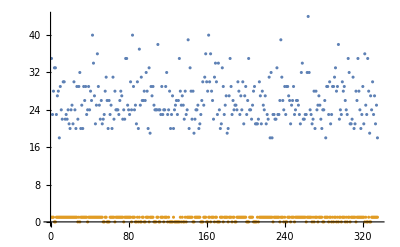

```mathematica
ListPlot[Transpose[bC⟦2;;,{bMI,chemoResponse}⟧]]
```

```mathematica
bC[[2;;,Tstage]];
```

```mathematica
SpearmanRankTest[bC[[2;;,Nstage]],bC⟦2;;,chemoResponse⟧,"TestDataTable"]
```

| Statistic | P-Value
Spearman Rank | 0. | 1.

```mathematica
SpearmanRankTest[bC[[2;;,Tstage]],bC⟦2;;,chemoResponse⟧,"TestDataTable"]
```

| Statistic | P-Value
Spearman Rank | 0.111457 | 0.0414769

```mathematica
SpearmanRankTest[bC[[2;;,bMI]],bC⟦2;;,chemoResponse⟧,"TestDataTable"]
```

| Statistic | P-Value
Spearman Rank | 0.0463358 | 0.397905

```mathematica
SpearmanRankTest[bC[[2;;,menopause]],bC⟦2;;,chemoResponse⟧,"TestDataTable"]
```

| Statistic | P-Value
Spearman Rank | 0.0562772 | 0.304418

```mathematica
perModel=LogitModelFit[
bC⟦2;;,{bMI,chemoResponse}⟧,x,x]
```

FittedModel[1/(1+ⅇ^(-«20»-«21» x))]

```mathematica
perModel["Properties"];
```

```mathematica
perModel["BestFit"];
```

```mathematica
perModel["ParameterTable"]
```

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.301508 | 0.706321 | 0.426871 | 0.669473
x | 0.0241027 | 0.0269406 | 0.894661 | 0.370969

```mathematica
perModel["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
1 | 0.301508 | 0.706321 | {-1.08286,1.68587}
x | 0.0241027 | 0.0269406 | {-0.0286999,0.0769052}

```mathematica
perModelM=LogitModelFit[bC⟦2;;,{menopause,chemoResponse}⟧,x,x]
```

FittedModel[1/(1+ⅇ^(-«18»-«19» x))]

```mathematica
perModelM["ParameterTable"]
```

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.561186 | 0.372298 | 1.50736 | 0.131719
x | 0.251762 | 0.244677 | 1.02896 | 0.3035

```mathematica
perModel["ParameterTableEntries"]
```

{{0.301508,0.706321,0.426871,0.669473},{0.0241027,0.0269406,0.894661,0.370969}}

The coefficient estimate is the first value on the second row of the table:

```mathematica
perModel["ParameterTableEntries"]⟦2,1⟧
```

0.0241027

The exponential of this value is an estimate of how much each menopause decreases the chances (that is, the odds) of having pathologic complete response

```mathematica
(Exp[perModel["ParameterTableEntries"]⟦2,1⟧])
```

1.0244

******So if we were to describe the result of the fitting in words, we could say that on average, every extra mass of bmi decreases the odds of a random patient having had a pathologic complete response by a factor of 1.0244.

```mathematica
bmichem=LogitModelFit[bC⟦2;;,{bMI,chemoResponse}⟧,x,x]
bmichem["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«21» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.301508 | 0.706321 | 0.426871 | 0.669473
x | 0.0241027 | 0.0269406 | 0.894661 | 0.370969

```mathematica
menchem=LogitModelFit[bC⟦2;;,{menopause,chemoResponse}⟧,x,x]
menchem["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«18»-«19» x))]

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.561186 | 0.372298 | 1.50736 | 0.131719
x | 0.251762 | 0.244677 | 1.02896 | 0.3035

```mathematica
bMI63=LogitModelFit[bC⟦2;;,{bMI,M63,chemoResponse}⟧,{1,x,xM63},
{x,xM63}]
bMI63["BestFit"]
bMI63["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»+«21» xM63))]

1/(1+ⅇ^(-0.382653-0.0242896 x+0.00928377 xM63))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.382653 | 0.716946 | 0.533726 | 0.593531
x | 0.0242896 | 0.0270038 | 0.899485 | 0.368394
xM63 | -0.00928377 | 0.0128849 | -0.720518 | 0.471206

```mathematica
bMI64=LogitModelFit[bC⟦2;;,{bMI,M64,chemoResponse}⟧,{1,x,xM64},
{x,xM64}]
bMI64["BestFit"]
bMI64["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»+«21» xM64))]

1/(1+ⅇ^(-0.414493-0.0234232 x+0.00943427 xM64))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.414493 | 0.723664 | 0.57277 | 0.5668
x | 0.0234232 | 0.0270332 | 0.866458 | 0.386239
xM64 | -0.00943427 | 0.0121521 | -0.776349 | 0.437543

```mathematica
bMI65=LogitModelFit[bC⟦2;;,{bMI,M65,chemoResponse}⟧,{1,x,xM65},
{x,xM65}]
bMI65["BestFit"]
bMI65["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»-«23» xM65))]

1/(1+ⅇ^(-0.28145-0.0240449 x-0.000182892 xM65))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.28145 | 0.715118 | 0.393571 | 0.693898
x | 0.0240449 | 0.0269291 | 0.892899 | 0.371912
xM65 | 0.000182892 | 0.0010426 | 0.17542 | 0.86075

```mathematica
bMI66=LogitModelFit[bC⟦2;;,{bMI,M66,chemoResponse}⟧,{1,x,xM66},
{x,xM66}]
bMI66["BestFit"]
bMI66["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«19»-«1»-«21» xM66))]

1/(1+ⅇ^(-0.262389-0.0231274 x-0.00838651 xM66))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.262389 | 0.710571 | 0.369265 | 0.71193
x | 0.0231274 | 0.026989 | 0.856921 | 0.391489
xM66 | 0.00838651 | 0.017279 | 0.485359 | 0.627421

```mathematica
bMI67=LogitModelFit[bC⟦2;;,{bMI,M67,chemoResponse}⟧,{1,x,xM67},
{x,xM67}]
bMI67["BestFit"]
bMI67["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«19»-«1»-«22» xM67))]

1/(1+ⅇ^(-0.297775-0.0241145 x-0.00048366 xM67))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.297775 | 0.71665 | 0.41551 | 0.677769
x | 0.0241145 | 0.0269424 | 0.895039 | 0.370766
xM67 | 0.00048366 | 0.0157388 | 0.0307305 | 0.975484

```mathematica
bMI68=LogitModelFit[bC⟦2;;,{bMI,M68,chemoResponse}⟧,{1,x,xM68},
{x,xM68}]
bMI68["BestFit"]
bMI68["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»+«21» xM68))]

1/(1+ⅇ^(-0.332903-0.0240422 x+0.00455375 xM68))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.332903 | 0.717013 | 0.464291 | 0.642439
x | 0.0240422 | 0.0269586 | 0.89182 | 0.37249
xM68 | -0.00455375 | 0.0174668 | -0.260709 | 0.794317

```mathematica
bMI69=LogitModelFit[bC⟦2;;,{bMI,M69,chemoResponse}⟧,{1,x,xM69},
{x,xM69}]
bMI69["BestFit"]
bMI69["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«19»-«1»-«21» xM69))]

1/(1+ⅇ^(-0.23342-0.0238889 x-0.00857395 xM69))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.23342 | 0.732854 | 0.318509 | 0.750099
x | 0.0238889 | 0.0269183 | 0.887459 | 0.374832
xM69 | 0.00857395 | 0.0249915 | 0.343074 | 0.731543

```mathematica
bMI70=LogitModelFit[bC⟦2;;,{bMI,M70,chemoResponse}⟧,{1,x,xM70},
{x,xM70}]
bMI70["BestFit"]
bMI70["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(«19»-«1»-«21» xM70))]

1/(1+ⅇ^(0.546281-0.0237894 x-0.0139706 xM70))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.546281 | 0.849654 | -0.642944 | 0.52026
x | 0.0237894 | 0.0270194 | 0.880453 | 0.378614
xM70 | 0.0139706 | 0.00776068 | 1.80017 | 0.0718331

```mathematica
bMI71=LogitModelFit[bC⟦2;;,{bMI,M71,chemoResponse}⟧,{1,x,xM71},
{x,xM71}]
bMI71["BestFit"]
bMI71["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«19»-«1»-«22» xM71))]

1/(1+ⅇ^(-0.281316-0.0237097 x-0.00250947 xM71))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.281316 | 0.724931 | 0.388059 | 0.697972
x | 0.0237097 | 0.027118 | 0.874314 | 0.381948
xM71 | 0.00250947 | 0.0203788 | 0.123141 | 0.901995

```mathematica
bMI72=LogitModelFit[bC⟦2;;,{bMI,M72,chemoResponse}⟧,{1,x,xM72},
{x,xM72}]
bMI72["BestFit"]
bMI72["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«19»-«1»-«21» xM72))]

1/(1+ⅇ^(-0.1197-0.0206419 x-0.0126753 xM72))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.1197 | 0.729067 | 0.164182 | 0.869588
x | 0.0206419 | 0.0271355 | 0.760699 | 0.446837
xM72 | 0.0126753 | 0.0124884 | 1.01497 | 0.310122

```mathematica
bMI73=LogitModelFit[bC⟦2;;,{bMI,M73,chemoResponse}⟧,{1,x,xM73},
{x,xM73}]
bMI73["BestFit"]
bMI73["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«19»-«1»-«21» xM73))]

1/(1+ⅇ^(-0.259761-0.02205 x-0.0163785 xM73))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.259761 | 0.730144 | 0.355767 | 0.722015
x | 0.02205 | 0.0283992 | 0.77643 | 0.437495
xM73 | 0.0163785 | 0.0730825 | 0.22411 | 0.822672

```mathematica
bMI74=LogitModelFit[bC⟦2;;,{bMI,M74,chemoResponse}⟧,{1,x,xM74},
{x,xM74}]
bMI74["BestFit"]
bMI74["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«19»-«1»+«21» xM74))]

1/(1+ⅇ^(-0.345923-0.0242192 x+0.00499872 xM74))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.345923 | 0.722396 | 0.478855 | 0.632042
x | 0.0242192 | 0.0269645 | 0.898189 | 0.369085
xM74 | -0.00499872 | 0.0167277 | -0.298829 | 0.765071

```mathematica
bMI75=LogitModelFit[bC⟦2;;,{bMI,M75,chemoResponse}⟧,{1,x,xM75},
{x,xM75}]
bMI75["BestFit"]
bMI75["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»-«21» xM75))]

1/(1+ⅇ^(-0.097003-0.0242557 x-0.011616 xM75))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.097003 | 0.742261 | 0.130686 | 0.896024
x | 0.0242557 | 0.0269569 | 0.899796 | 0.368229
xM75 | 0.011616 | 0.0129993 | 0.893587 | 0.371543

```mathematica
bMI76=LogitModelFit[bC⟦2;;,{bMI,M76,chemoResponse}⟧,{1,x,xM76},
{x,xM76}]
bMI76["BestFit"]
bMI76["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«19»-«1»-«20» xM76))]

1/(1+ⅇ^(-0.201598-0.0230883 x-0.0249931 xM76))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.201598 | 0.744624 | 0.270738 | 0.786593
x | 0.0230883 | 0.0270202 | 0.854483 | 0.392838
xM76 | 0.0249931 | 0.0593886 | 0.420841 | 0.673871

```mathematica
bMI77=LogitModelFit[bC⟦2;;,{bMI,M77,chemoResponse}⟧,{1,x,xM77},
{x,xM77}]
bMI77["BestFit"]
bMI77["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»+«21» xM77))]

1/(1+ⅇ^(-0.326685-0.0241265 x+0.00536476 xM77))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.326685 | 0.752181 | 0.434317 | 0.664058
x | 0.0241265 | 0.0269517 | 0.895175 | 0.370693
xM77 | -0.00536476 | 0.054911 | -0.0976992 | 0.922171

```mathematica
bMI78=LogitModelFit[bC⟦2;;,{bMI,M78,chemoResponse}⟧,{1,x,xM78},
{x,xM78}]
bMI78["BestFit"]
bMI78["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»-«21» xM78))]

1/(1+ⅇ^(-0.208064-0.0239858 x-0.00321612 xM78))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.208064 | 0.743009 | 0.280028 | 0.779456
x | 0.0239858 | 0.0269487 | 0.890055 | 0.373436
xM78 | 0.00321612 | 0.00794938 | 0.404575 | 0.68579

```mathematica
bMI79=LogitModelFit[bC⟦2;;,{bMI,M79,chemoResponse}⟧,{1,x,xM79},
{x,xM79}]
bMI79["BestFit"]
bMI79["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»-«21» xM79))]

1/(1+ⅇ^(-0.117853-0.0241434 x-0.0099126 xM79))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.117853 | 0.742764 | 0.158668 | 0.873931
x | 0.0241434 | 0.0269434 | 0.896076 | 0.370212
xM79 | 0.0099126 | 0.0124709 | 0.794861 | 0.426695

```mathematica
bMI80=LogitModelFit[bC⟦2;;,{bMI,M80,chemoResponse}⟧,{1,x,xM80},
{x,xM80}]
bMI80["BestFit"]
bMI80["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«18»-«1»-«20» xM80))]

1/(1+ⅇ^(-0.171517-0.0237405 x-0.047455 xM80))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.171517 | 0.804056 | 0.213315 | 0.831081
x | 0.0237405 | 0.0269535 | 0.880795 | 0.378429
xM80 | 0.047455 | 0.14037 | 0.33807 | 0.735311

```mathematica
bMI81=LogitModelFit[bC⟦2;;,{bMI,M81,chemoResponse}⟧,{1,x,xM81},
{x,xM81}]
bMI81["BestFit"]
bMI81["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»-«22» xM81))]

1/(1+ⅇ^(-0.2759-0.0240128 x-0.00266014 xM81))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.2759 | 0.7429 | 0.371383 | 0.710352
x | 0.0240128 | 0.0269448 | 0.891184 | 0.372831
xM81 | 0.00266014 | 0.0240083 | 0.110801 | 0.911774

```mathematica
bMI82=LogitModelFit[bC⟦2;;,{bMI,M82,chemoResponse}⟧,{1,x,xM82},
{x,xM82}]
bMI82["BestFit"]
bMI82["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»+«21» xM82))]

1/(1+ⅇ^(-0.441326-0.0243957 x+0.0173569 xM82))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.441326 | 0.751532 | 0.587235 | 0.557046
x | 0.0243957 | 0.027018 | 0.902943 | 0.366556
xM82 | -0.0173569 | 0.0312002 | -0.556309 | 0.578

```mathematica
bMI83=LogitModelFit[bC⟦2;;,{bMI,M83,chemoResponse}⟧,{1,x,xM83},
{x,xM83}]
bMI83["BestFit"]
bMI83["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»-«20» xM83))]

1/(1+ⅇ^(-0.249944-0.0238586 x-0.030906 xM83))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.249944 | 0.718308 | 0.347962 | 0.727869
x | 0.0238586 | 0.0269219 | 0.886213 | 0.375503
xM83 | 0.030906 | 0.0807351 | 0.382807 | 0.701863

```mathematica
bMI84=LogitModelFit[bC⟦2;;,{bMI,M84,chemoResponse}⟧,{1,x,xM84},
{x,xM84}]
bMI84["BestFit"]
bMI84["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»-«21» xM84))]

1/(1+ⅇ^(-0.119948-0.024708 x-0.0112938 xM84))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.119948 | 0.758072 | 0.158228 | 0.874277
x | 0.024708 | 0.0269572 | 0.916564 | 0.359371
xM84 | 0.0112938 | 0.0173108 | 0.652414 | 0.514134

```mathematica
bMI85=LogitModelFit[bC⟦2;;,{bMI,M85,chemoResponse}⟧,{1,x,xM85},
{x,xM85}]
bMI85["BestFit"]
bMI85["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«17»-«1»-«21» xM85))]

1/(1+ⅇ^(-0.118728-0.0232233 x-0.00392371 xM85))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.118728 | 0.742018 | 0.160007 | 0.872876
x | 0.0232233 | 0.0269682 | 0.861136 | 0.389163
xM85 | 0.00392371 | 0.00488355 | 0.803456 | 0.421711

```mathematica
bMI86=LogitModelFit[bC⟦2;;,{bMI,M86,chemoResponse}⟧,{1,x,xM86},
{x,xM86}]
bMI86["BestFit"]
bMI86["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«19»-«1»+«19» xM86))]

1/(1+ⅇ^(-0.325584-0.0241662 x+0.0331096 xM86))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.325584 | 0.728265 | 0.447067 | 0.654826
x | 0.0241662 | 0.0269579 | 0.896441 | 0.370017
xM86 | -0.0331096 | 0.242009 | -0.136811 | 0.89118

```mathematica
bMI87=LogitModelFit[bC⟦2;;,{bMI,M87,chemoResponse}⟧,{1,x,xM87},
{x,xM87}]
bMI87["BestFit"]
bMI87["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»-«21» xM87))]

1/(1+ⅇ^(-0.260228-0.0195328 x-0.015562 xM87))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.260228 | 0.705389 | 0.368914 | 0.712192
x | 0.0195328 | 0.0270201 | 0.7229 | 0.469742
xM87 | 0.015562 | 0.01045 | 1.48918 | 0.13644

```mathematica
bMI88=LogitModelFit[bC⟦2;;,{bMI,M88,chemoResponse}⟧,{1,x,xM88},
{x,xM88}]
bMI88["BestFit"]
bMI88["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«19»-«1»-«21» xM88))]

1/(1+ⅇ^(-0.302254-0.0130326 x-0.0218635 xM88))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.302254 | 0.703342 | 0.429739 | 0.667385
x | 0.0130326 | 0.0272142 | 0.478888 | 0.632018
xM88 | 0.0218635 | 0.0109996 | 1.98765 | 0.0468501

```mathematica
bMI89=LogitModelFit[bC⟦2;;,{bMI,M89,chemoResponse}⟧,{1,x,xM89},
{x,xM89}]
bMI89["BestFit"]
bMI89["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«18»-«1»-«21» xM89))]

1/(1+ⅇ^(-0.23429-0.0139975 x-0.00514728 xM89))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.23429 | 0.70571 | 0.331992 | 0.739896
x | 0.0139975 | 0.0272452 | 0.513761 | 0.607419
xM89 | 0.00514728 | 0.00261236 | 1.97036 | 0.0487972

```mathematica
bMI90=LogitModelFit[bC⟦2;;,{bMI,M90,chemoResponse}⟧,{1,x,xM90},
{x,xM90}]
bMI90["BestFit"]
bMI90["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»-«22» xM90))]

1/(1+ⅇ^(-0.300736-0.0135562 x-0.00310512 xM90))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.300736 | 0.704922 | 0.426623 | 0.669654
x | 0.0135562 | 0.027368 | 0.49533 | 0.620368
xM90 | 0.00310512 | 0.00179595 | 1.72895 | 0.0838172

```mathematica
bMI91=LogitModelFit[bC⟦2;;,{bMI,M91,chemoResponse}⟧,{1,x,xM91},
{x,xM91}]
bMI91["BestFit"]
bMI91["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«19»-«1»-«21» xM91))]

1/(1+ⅇ^(-0.331897-0.0106588 x-0.0451898 xM91))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.331897 | 0.703115 | 0.472038 | 0.6369
x | 0.0106588 | 0.027223 | 0.391536 | 0.695401
xM91 | 0.0451898 | 0.0197504 | 2.28805 | 0.0221348

```mathematica
bMI92=LogitModelFit[bC⟦2;;,{bMI,M92,chemoResponse}⟧,{1,x,xM92},
{x,xM92}]
bMI92["BestFit"]
bMI92["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«19»-«1»-«20» xM92))]

1/(1+ⅇ^(-0.275972-0.0133219 x-0.219369 xM92))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.275972 | 0.705071 | 0.39141 | 0.695494
x | 0.0133219 | 0.027126 | 0.491111 | 0.623348
xM92 | 0.219369 | 0.101888 | 2.15303 | 0.031316

```mathematica
bMI93=LogitModelFit[bC⟦2;;,{bMI,M93,chemoResponse}⟧,{1,x,xM93},
{x,xM93}]
bMI93["BestFit"]
bMI93["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«19»-«1»-«21» xM93))]

1/(1+ⅇ^(-0.343468-0.00413041 x-0.0125526 xM93))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.343468 | 0.703557 | 0.488188 | 0.625417
x | 0.00413041 | 0.0274945 | 0.150227 | 0.880586
xM93 | 0.0125526 | 0.00474427 | 2.64585 | 0.00814848

```mathematica
bMI94=LogitModelFit[bC⟦2;;,{bMI,M94,chemoResponse}⟧,{1,x,xM94},
{x,xM94}]
bMI94["BestFit"]
bMI94["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«18»-«1»+«21» xM94))]

1/(1+ⅇ^(-0.33998-0.0242778 x+0.00930501 xM94))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.33998 | 0.713494 | 0.476499 | 0.633719
x | 0.0242778 | 0.0269609 | 0.900481 | 0.367865
xM94 | -0.00930501 | 0.0235921 | -0.394411 | 0.693277

```mathematica
bMI95=LogitModelFit[bC⟦2;;,{bMI,M95,chemoResponse}⟧,{1,x,xM95},
{x,xM95}]
bMI95["BestFit"]
bMI95["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«19»-«1»-«22» xM95))]

1/(1+ⅇ^(-0.329193-0.00931624 x-0.00394018 xM95))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.329193 | 0.705601 | 0.466543 | 0.640827
x | 0.00931624 | 0.027498 | 0.338798 | 0.734762
xM95 | 0.00394018 | 0.00186053 | 2.11777 | 0.0341942

```mathematica
bMI96=LogitModelFit[bC⟦2;;,{bMI,M96,chemoResponse}⟧,{1,x,xM96},
{x,xM96}]
bMI96["BestFit"]
bMI96["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«19»-«1»-«22» xM96))]

1/(1+ⅇ^(-0.26683-0.0172842 x-0.000715166 xM96))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.26683 | 0.706524 | 0.377666 | 0.705679
x | 0.0172842 | 0.0272126 | 0.635153 | 0.525329
xM96 | 0.000715166 | 0.00048021 | 1.48928 | 0.136414

```mathematica
bMI97=LogitModelFit[bC⟦2;;,{bMI,M97,chemoResponse}⟧,{1,x,xM97},
{x,xM97}]
bMI97["BestFit"]
bMI97["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»-«21» xM97))]

1/(1+ⅇ^(-0.229397-0.00876105 x-0.0151389 xM97))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.229397 | 0.709663 | 0.323248 | 0.746507
x | 0.00876105 | 0.0273663 | 0.32014 | 0.748862
xM97 | 0.0151389 | 0.00599157 | 2.52671 | 0.0115137

```mathematica
bMI98=LogitModelFit[bC⟦2;;,{bMI,M98,chemoResponse}⟧,{1,x,xM98},
{x,xM98}]
bMI98["BestFit"]
bMI98["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(«18»-«1»-«22» xM98))]

1/(1+ⅇ^(0.051757-0.00881667 x-0.00190235 xM98))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.051757 | 0.725555 | -0.0713344 | 0.943132
x | 0.00881667 | 0.0275212 | 0.320359 | 0.748696
xM98 | 0.00190235 | 0.000761702 | 2.4975 | 0.0125074

```mathematica
bMI99=LogitModelFit[bC⟦2;;,{bMI,M99,chemoResponse}⟧,{1,x,xM99},
{x,xM99}]
bMI99["BestFit"]
bMI99["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»-«20» xM99))]

1/(1+ⅇ^(-0.19724-0.0107404 x-0.130415 xM99))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.19724 | 0.705961 | 0.279393 | 0.779943
x | 0.0107404 | 0.0274403 | 0.39141 | 0.695494
xM99 | 0.130415 | 0.0669134 | 1.94901 | 0.0512944

```mathematica
bMI100=LogitModelFit[bC⟦2;;,{bMI,M100,chemoResponse}⟧,{1,x,xM100},
{x,xM100}]
bMI100["BestFit"]
bMI100["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»-«20» «5»))]

1/(1+ⅇ^(-0.0835534-0.0167388 x-0.140841 xM100))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.0835534 | 0.715929 | 0.116706 | 0.907093
x | 0.0167388 | 0.0271556 | 0.616402 | 0.537629
xM100 | 0.140841 | 0.0721943 | 1.95086 | 0.0510742

```mathematica
bMI101=LogitModelFit[bC⟦2;;,{bMI,M101,chemoResponse}⟧,{1,x,xM101},
{x,xM101}]
bMI101["BestFit"]
bMI101["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(«21»-«1»-«21» «5»))]

1/(1+ⅇ^(0.00859308-0.0108977 x-0.00609769 xM101))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.00859308 | 0.72498 | -0.0118528 | 0.990543
x | 0.0108977 | 0.0275387 | 0.395723 | 0.692309
xM101 | 0.00609769 | 0.00218241 | 2.79402 | 0.00520567

```mathematica
bMI102=LogitModelFit[bC⟦2;;,{bMI,M102,chemoResponse}⟧,{1,x,xM102},
{x,xM102}]
bMI102["BestFit"]
bMI102["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»-«21» «5»))]

1/(1+ⅇ^(-0.100608-0.0100971 x-0.0107974 xM102))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.100608 | 0.72386 | 0.138988 | 0.88946
x | 0.0100971 | 0.0274335 | 0.368055 | 0.712832
xM102 | 0.0107974 | 0.0042789 | 2.52341 | 0.0116222

```mathematica
bMI103=LogitModelFit[bC⟦2;;,{bMI,M103,chemoResponse}⟧,{1,x,xM103},
{x,xM103}]
bMI103["BestFit"]
bMI103["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«21»-«1»-«19» «5»))]

1/(1+ⅇ^(-0.0290403-0.0131892 x-0.304708 xM103))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.0290403 | 0.72484 | 0.0400644 | 0.968042
x | 0.0131892 | 0.0272482 | 0.484039 | 0.628358
xM103 | 0.304708 | 0.114158 | 2.66919 | 0.0076035

```mathematica
bMI104=LogitModelFit[bC⟦2;;,{bMI,M104,chemoResponse}⟧,{1,x,xM104},
{x,xM104}]
bMI104["BestFit"]
bMI104["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»-«22» «5»))]

1/(1+ⅇ^(-0.0529833-0.018434 x-0.00665566 xM104))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.0529833 | 0.721591 | 0.0734257 | 0.941467
x | 0.018434 | 0.0271367 | 0.679303 | 0.496946
xM104 | 0.00665566 | 0.0028716 | 2.31776 | 0.0204626

```mathematica
bMI105=LogitModelFit[bC⟦2;;,{bMI,M105,chemoResponse}⟧,{1,x,xM105},
{x,xM105}]
bMI105["BestFit"]
bMI105["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»-«20» «5»))]

1/(1+ⅇ^(-0.15598-0.0231561 x-0.0536425 xM105))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.15598 | 0.711594 | 0.219198 | 0.826496
x | 0.0231561 | 0.0269984 | 0.857686 | 0.391066
xM105 | 0.0536425 | 0.0313739 | 1.70978 | 0.0873065

```mathematica
bMI106=LogitModelFit[bC⟦2;;,{bMI,M106,chemoResponse}⟧,{1,x,xM106},
{x,xM106}]
bMI106["BestFit"]
bMI106["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»-«20» «5»))]

1/(1+ⅇ^(-0.149459-0.0225548 x-0.124615 xM106))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.149459 | 0.712395 | 0.209798 | 0.833825
x | 0.0225548 | 0.0270491 | 0.833847 | 0.404367
xM106 | 0.124615 | 0.0627588 | 1.98561 | 0.0470761

```mathematica
bMI107=LogitModelFit[bC⟦2;;,{bMI,M107,chemoResponse}⟧,{1,x,xM107},
{x,xM107}]
bMI107["BestFit"]
bMI107["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»-«21» «5»))]

1/(1+ⅇ^(-0.151411-0.0216601 x-0.0251283 xM107))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.151411 | 0.709983 | 0.21326 | 0.831124
x | 0.0216601 | 0.0269591 | 0.803445 | 0.421718
xM107 | 0.0251283 | 0.0137951 | 1.82154 | 0.0685245

```mathematica
bMI108=LogitModelFit[bC⟦2;;,{bMI,M108,chemoResponse}⟧,{1,x,xM108},
{x,xM108}]
bMI108["BestFit"]
bMI108["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«19»-«1»-«20» «5»))]

1/(1+ⅇ^(-0.170773-0.0212106 x-0.0345509 xM108))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.170773 | 0.709406 | 0.240727 | 0.809767
x | 0.0212106 | 0.026994 | 0.785753 | 0.432012
xM108 | 0.0345509 | 0.0177533 | 1.94617 | 0.0516347

```mathematica
bMI109=LogitModelFit[bC⟦2;;,{bMI,M109,chemoResponse}⟧,{1,x,xM109},
{x,xM109}]
bMI109["BestFit"]
bMI109["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«19»-«1»-«20» «5»))]

1/(1+ⅇ^(-0.139524-0.0221141 x-0.117898 xM109))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.139524 | 0.710451 | 0.196388 | 0.844306
x | 0.0221141 | 0.0269396 | 0.820877 | 0.411716
xM109 | 0.117898 | 0.0608171 | 1.93856 | 0.0525551

```mathematica
bMI110=LogitModelFit[bC⟦2;;,{bMI,M110,chemoResponse}⟧,{1,x,xM110},
{x,xM110}]
bMI110["BestFit"]
bMI110["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»-«19» «5»))]

1/(1+ⅇ^(-0.174293-0.0218281 x-0.13487 xM110))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.174293 | 0.71348 | 0.244286 | 0.807009
x | 0.0218281 | 0.0269423 | 0.81018 | 0.417837
xM110 | 0.13487 | 0.121864 | 1.10672 | 0.268416

```mathematica
bMI111=LogitModelFit[bC⟦2;;,{bMI,M111,chemoResponse}⟧,{1,x,xM111},
{x,xM111}]
bMI111["BestFit"]
bMI111["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»-«20» «5»))]

1/(1+ⅇ^(-0.14336-0.0187094 x-0.014576 xM111))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.14336 | 0.710119 | 0.201882 | 0.840009
x | 0.0187094 | 0.0270466 | 0.691749 | 0.489095
xM111 | 0.014576 | 0.00650566 | 2.24051 | 0.0250575

```mathematica
bMI112=LogitModelFit[bC⟦2;;,{bMI,M112,chemoResponse}⟧,{1,x,xM112},
{x,xM112}]
bMI112["BestFit"]
bMI112["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»-«19» «5»))]

1/(1+ⅇ^(-0.0854025-0.0207919 x-0.0401292 xM112))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.0854025 | 0.711506 | 0.120031 | 0.904459
x | 0.0207919 | 0.026969 | 0.770955 | 0.440733
xM112 | 0.0401292 | 0.0166482 | 2.41042 | 0.0159342

```mathematica
bMI113=LogitModelFit[bC⟦2;;,{bMI,M113,chemoResponse}⟧,{1,x,xM113},
{x,xM113}]
bMI113["BestFit"]
bMI113["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»-«20» «5»))]

1/(1+ⅇ^(-0.199174-0.0206654 x-0.0811975 xM113))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.199174 | 0.709297 | 0.280804 | 0.778861
x | 0.0206654 | 0.0269896 | 0.765681 | 0.443866
xM113 | 0.0811975 | 0.0683276 | 1.18836 | 0.234693

```mathematica
bMI114=LogitModelFit[bC⟦2;;,{bMI,M114,chemoResponse}⟧,{1,x,xM114},
{x,xM114}]
bMI114["BestFit"]
bMI114["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»-«20» «5»))]

1/(1+ⅇ^(-0.193898-0.0181056 x-0.0720684 xM114))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.193898 | 0.70697 | 0.274266 | 0.78388
x | 0.0181056 | 0.0270457 | 0.669444 | 0.503212
xM114 | 0.0720684 | 0.0420471 | 1.71399 | 0.0865301

```mathematica
bMI115=LogitModelFit[bC⟦2;;,{bMI,M115,chemoResponse}⟧,{1,x,xM115},
{x,xM115}]
bMI115["BestFit"]
bMI115["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»-«21» «5»))]

1/(1+ⅇ^(-0.170878-0.0145119 x-0.0108489 xM115))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.170878 | 0.707022 | 0.241687 | 0.809023
x | 0.0145119 | 0.0270863 | 0.535765 | 0.592121
xM115 | 0.0108489 | 0.0048168 | 2.2523 | 0.0243035

```mathematica
bMI116=LogitModelFit[bC⟦2;;,{bMI,M116,chemoResponse}⟧,{1,x,xM116},
{x,xM116}]
bMI116["BestFit"]
bMI116["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«21»-«1»-«20» «5»))]

1/(1+ⅇ^(-0.0560699-0.0198973 x-0.0337991 xM116))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.0560699 | 0.713139 | 0.0786241 | 0.937332
x | 0.0198973 | 0.0269382 | 0.738626 | 0.460134
xM116 | 0.0337991 | 0.0142547 | 2.37109 | 0.0177359

```mathematica
bMI117=LogitModelFit[bC⟦2;;,{bMI,M117,chemoResponse}⟧,{1,x,xM117},
{x,xM117}]
bMI117["BestFit"]
bMI117["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»-«20» «5»))]

1/(1+ⅇ^(-0.228103-0.0177356 x-0.105738 xM117))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.228103 | 0.705515 | 0.323314 | 0.746457
x | 0.0177356 | 0.0271503 | 0.653239 | 0.513602
xM117 | 0.105738 | 0.0749607 | 1.41059 | 0.158367

```mathematica
bMI118=LogitModelFit[bC⟦2;;,{bMI,M118,chemoResponse}⟧,{1,x,xM118},
{x,xM118}]
bMI118["BestFit"]
bMI118["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»-«21» «5»))]

1/(1+ⅇ^(-0.245994-0.0154086 x-0.0307312 xM118))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.245994 | 0.705804 | 0.34853 | 0.727442
x | 0.0154086 | 0.0272517 | 0.565417 | 0.57179
xM118 | 0.0307312 | 0.0178764 | 1.7191 | 0.0855967

```mathematica
bMI119=LogitModelFit[bC⟦2;;,{bMI,M119,chemoResponse}⟧,{1,x,xM119},
{x,xM119}]
bMI119["BestFit"]
bMI119["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»-«21» «5»))]

1/(1+ⅇ^(-0.183728-0.0165505 x-0.0473953 xM119))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.183728 | 0.707004 | 0.259868 | 0.794966
x | 0.0165505 | 0.0271415 | 0.609788 | 0.542003
xM119 | 0.0473953 | 0.0294924 | 1.60704 | 0.108046

```mathematica
bMI120=LogitModelFit[bC⟦2;;,{bMI,M120,chemoResponse}⟧,{1,x,xM120},
{x,xM120}]
bMI120["BestFit"]
bMI120["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»-«20» «5»))]

1/(1+ⅇ^(-0.242661-0.0216445 x-0.0923717 xM120))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.242661 | 0.707448 | 0.343009 | 0.731592
x | 0.0216445 | 0.0269736 | 0.802432 | 0.422303
xM120 | 0.0923717 | 0.0905 | 1.02068 | 0.307406

```mathematica
bMI121=LogitModelFit[bC⟦2;;,{bMI,M121,chemoResponse}⟧,{1,x,xM121},
{x,xM121}]
bMI121["BestFit"]
bMI121["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»-«21» «5»))]

1/(1+ⅇ^(-0.0893824-0.00490234 x-0.010096 xM121))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.0893824 | 0.713538 | 0.125267 | 0.900313
x | 0.00490234 | 0.0276645 | 0.177207 | 0.859346
xM121 | 0.010096 | 0.00353336 | 2.85734 | 0.00427202

```mathematica
bMI122=LogitModelFit[bC⟦2;;,{bMI,M122,chemoResponse}⟧,{1,x,xM122},
{x,xM122}]
bMI122["BestFit"]
bMI122["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»-«21» «5»))]

1/(1+ⅇ^(-0.0808122-0.018704 x-0.0392072 xM122))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.0808122 | 0.714122 | 0.113163 | 0.909901
x | 0.018704 | 0.0270741 | 0.690844 | 0.489663
xM122 | 0.0392072 | 0.0178157 | 2.20071 | 0.0277563

```mathematica
bMI123=LogitModelFit[bC⟦2;;,{bMI,M123,chemoResponse}⟧,{1,x,xM123},
{x,xM123}]
bMI123["BestFit"]
bMI123["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»-«20» «5»))]

1/(1+ⅇ^(-0.0970997-0.0231607 x-0.204994 xM123))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.0970997 | 0.714633 | 0.135873 | 0.891921
x | 0.0231607 | 0.0268928 | 0.861221 | 0.389116
xM123 | 0.204994 | 0.13235 | 1.54888 | 0.121411

```mathematica
bMI124=LogitModelFit[bC⟦2;;,{bMI,M124,chemoResponse}⟧,{1,x,xM124},
{x,xM124}]
bMI124["BestFit"]
bMI124["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»-«21» «5»))]

1/(1+ⅇ^(-0.192536-0.00939784 x-0.0281836 xM124))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.192536 | 0.706944 | 0.27235 | 0.785353
x | 0.00939784 | 0.0276629 | 0.339727 | 0.734062
xM124 | 0.0281836 | 0.0138764 | 2.03105 | 0.0422498

```mathematica
bMI125=LogitModelFit[bC⟦2;;,{bMI,M125,chemoResponse}⟧,{1,x,xM125},
{x,xM125}]
bMI125["BestFit"]
bMI125["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«19»-«1»-«19» «5»))]

1/(1+ⅇ^(-0.154065-0.0141397 x-0.0388437 xM125))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.154065 | 0.71145 | 0.216551 | 0.828558
x | 0.0141397 | 0.0272896 | 0.518138 | 0.604362
xM125 | 0.0388437 | 0.0191413 | 2.02931 | 0.0424264

```mathematica
bMI126=LogitModelFit[bC⟦2;;,{bMI,M126,chemoResponse}⟧,{1,x,xM126},
{x,xM126}]
bMI126["BestFit"]
bMI126["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»-«20» «5»))]

1/(1+ⅇ^(-0.10902-0.0178128 x-0.203491 xM126))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.10902 | 0.713632 | 0.152768 | 0.878581
x | 0.0178128 | 0.0271015 | 0.657264 | 0.511011
xM126 | 0.203491 | 0.105261 | 1.93321 | 0.0532109

```mathematica
bMI127=LogitModelFit[bC⟦2;;,{bMI,M127,chemoResponse}⟧,{1,x,xM127},
{x,xM127}]
bMI127["BestFit"]
bMI127["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»-«19» «5»))]

1/(1+ⅇ^(-0.143475-0.0195367 x-0.0199892 xM127))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.143475 | 0.710222 | 0.202014 | 0.839905
x | 0.0195367 | 0.0270613 | 0.721944 | 0.470329
xM127 | 0.0199892 | 0.0112349 | 1.77921 | 0.0752048

```mathematica
bMI128=LogitModelFit[bC⟦2;;,{bMI,M128,chemoResponse}⟧,{1,x,xM128},
{x,xM128}]
bMI128["BestFit"]
bMI128["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»-«21» «5»))]

1/(1+ⅇ^(-0.278262-0.0240559 x-0.014634 xM128))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.278262 | 0.70747 | 0.393319 | 0.694084
x | 0.0240559 | 0.0269286 | 0.893322 | 0.371685
xM128 | 0.014634 | 0.0344975 | 0.424205 | 0.671416

```mathematica
bMI129=LogitModelFit[bC⟦2;;,{bMI,M129,chemoResponse}⟧,{1,x,xM129},
{x,xM129}]
bMI129["BestFit"]
bMI129["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»-«19» «5»))]

1/(1+ⅇ^(-0.0636456-0.00771473 x-0.1128 xM129))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.0636456 | 0.715711 | 0.0889263 | 0.92914
x | 0.00771473 | 0.0274608 | 0.280936 | 0.77876
xM129 | 0.1128 | 0.0440118 | 2.56295 | 0.0103788

```mathematica
bMI130=LogitModelFit[bC⟦2;;,{bMI,M130,chemoResponse}⟧,{1,x,xM130},
{x,xM130}]
bMI130["BestFit"]
bMI130["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»-«21» «5»))]

1/(1+ⅇ^(-0.093463-0.0250745 x-0.0415173 xM130))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.093463 | 0.803422 | 0.116331 | 0.90739
x | 0.0250745 | 0.0270098 | 0.92835 | 0.353226
xM130 | 0.0415173 | 0.0764752 | 0.542885 | 0.587209

```mathematica
bMI131=LogitModelFit[bC⟦2;;,{bMI,M131,chemoResponse}⟧,{1,x,xM131},
{x,xM131}]
bMI131["BestFit"]
bMI131["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«19»-«1»-«20» «5»))]

1/(1+ⅇ^(-0.266373-0.0106396 x-0.103428 xM131))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.266373 | 0.707821 | 0.376328 | 0.706673
x | 0.0106396 | 0.0272701 | 0.390157 | 0.69642
xM131 | 0.103428 | 0.0393497 | 2.62844 | 0.00857782

```mathematica
bMI132=LogitModelFit[bC⟦2;;,{bMI,M132,chemoResponse}⟧,{1,x,xM132},
{x,xM132}]
bMI132["BestFit"]
bMI132["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«19»-«1»-«21» «5»))]

1/(1+ⅇ^(-0.395037-0.00158284 x-0.0214583 xM132))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.395037 | 0.704393 | 0.560819 | 0.574921
x | 0.00158284 | 0.0281446 | 0.0562396 | 0.955151
xM132 | 0.0214583 | 0.00921729 | 2.32805 | 0.0199097

```mathematica
bMI133=LogitModelFit[bC⟦2;;,{bMI,M133,chemoResponse}⟧,{1,x,xM133},
{x,xM133}]
bMI133["BestFit"]
bMI133["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«19»-«1»-«20» «5»))]

1/(1+ⅇ^(-0.340882-0.00690993 x-0.0385611 xM133))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.340882 | 0.703918 | 0.484265 | 0.628198
x | 0.00690993 | 0.0277616 | 0.248902 | 0.803437
xM133 | 0.0385611 | 0.0176282 | 2.18746 | 0.0287088

```mathematica
bMI134=LogitModelFit[bC⟦2;;,{bMI,M134,chemoResponse}⟧,{1,x,xM134},
{x,xM134}]
bMI134["BestFit"]
bMI134["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«18»-«1»-«21» «5»))]

1/(1+ⅇ^(-0.335351-0.0179172 x-0.0532615 xM134))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.335351 | 0.705169 | 0.475561 | 0.634387
x | 0.0179172 | 0.0276477 | 0.648053 | 0.51695
xM134 | 0.0532615 | 0.0598673 | 0.889659 | 0.373649

```mathematica
bMI135=LogitModelFit[bC⟦2;;,{bMI,M135,chemoResponse}⟧,{1,x,xM135},
{x,xM135}]
bMI135["BestFit"]
bMI135["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«19»-«1»-«20» «5»))]

1/(1+ⅇ^(-0.263566-0.0149804 x-0.0388571 xM135))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.263566 | 0.70687 | 0.372863 | 0.70925
x | 0.0149804 | 0.0275396 | 0.543958 | 0.58647
xM135 | 0.0388571 | 0.0269518 | 1.44172 | 0.14938

```mathematica
bMI136=LogitModelFit[bC⟦2;;,{bMI,M136,chemoResponse}⟧,{1,x,xM136},
{x,xM136}]
bMI136["BestFit"]
bMI136["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«19»-«1»-«21» «5»))]

1/(1+ⅇ^(-0.286885-0.0179293 x-0.0119913 xM136))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.286885 | 0.704485 | 0.407227 | 0.683841
x | 0.0179293 | 0.0277104 | 0.647023 | 0.517617
xM136 | 0.0119913 | 0.0137584 | 0.871566 | 0.383445

```mathematica
bMI137=LogitModelFit[bC⟦2;;,{bMI,M137,chemoResponse}⟧,{1,x,xM137},
{x,xM137}]
bMI137["BestFit"]
bMI137["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«20»-«1»-«22» «5»))]

1/(1+ⅇ^(-0.326632-0.0211099 x-0.00438107 xM137))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.326632 | 0.709308 | 0.460494 | 0.645162
x | 0.0211099 | 0.028247 | 0.747331 | 0.454864
xM137 | 0.00438107 | 0.0127696 | 0.343086 | 0.731533

```mathematica
bMI138=LogitModelFit[bC⟦2;;,{bMI,M138,chemoResponse}⟧,{1,x,xM138},
{x,xM138}]
bMI138["BestFit"]
bMI138["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«19»-«1»-«20» «5»))]

1/(1+ⅇ^(-0.211694-0.0176503 x-0.269137 xM138))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.211694 | 0.71022 | 0.298069 | 0.765651
x | 0.0176503 | 0.0273687 | 0.644907 | 0.518988
xM138 | 0.269137 | 0.23182 | 1.16097 | 0.245653

```mathematica
bmimet=Import["C:\\Users\\oreol\\Desktop\\proj\\bmiChemomet1.xlsx"];
bmimet2=Import["C:\\Users\\oreol\\Desktop\\proj\\bmiChemomet2.xlsx"];
```

```mathematica
bmimetdt=Flatten[bmimet,1];
bmimetdt2=Flatten[bmimet2,1];
Length[bmimetdt]
Length[bmimetdt2]
```

114

26

```mathematica
bmimetns=bmimetdt[[2;;,3]];
bmimets=bmimetdt2[[2;;,3]];
```

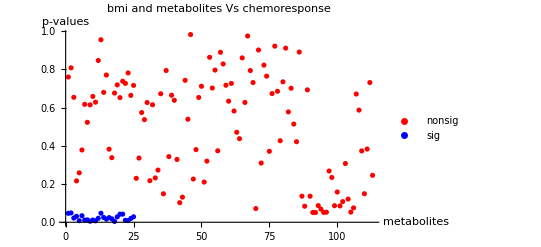

```mathematica
ListPlot[{bmimetns,bmimets},PlotLegends->{"nonsig","sig"},PlotStyle->{Red,Blue},PlotLabel->"bmi and metabolites Vs chemoresponse",AxesLabel->{"metabolites","p-values"}]
```

```mathematica
dtbmi=Transpose[bmimetdt];
dtbmi2=Transpose[bmimetdt2];
```

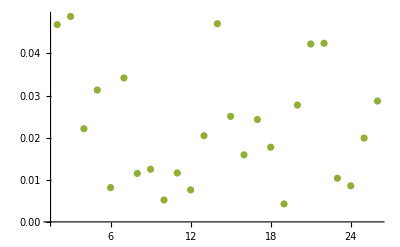

```mathematica
ListPlot[Tooltip[dtbmi2],PlotRange->Full]
```

```mathematica
bmimetdt2[[2;;,1]]
```

{M88,M89,M91,M92,M93,M95,M97,M98,M101,M102,M103,M104,M106,M111,M112,M115,M116,M121,M122,M124,M125,M129,M131,M132,M133}

```mathematica
bmilM=LogitModelFit[bC⟦2;;,{bMI,M88,M89,M91,M92,M93,M95,M97,M98,M101,M102,M103,M104,M106,M111,M112,M115,M116,M121,M122,M124,M125,M129,M131,M132,M133,chemoResponse}⟧,{1,x,xM88,xM89,xM91,xM92,xM93,xM95,xM97,xM98,xM101,xM102,xM103,xM104,xM106,xM111,xM112,xM115,xM116,xM121,xM122,xM124,xM125,xM129,xM131,xM132,xM133},
{x,xM88,xM89,xM91,xM92,xM93,xM95,xM97,xM98,xM101,xM102,xM103,xM104,xM106,xM111,xM112,xM115,xM116,xM121,xM122,xM124,xM125,xM129,xM131,xM132,xM133}]
bmilM["BestFit"]
bmilM["ParameterTable"]
bmilMent=bmilM["ParameterTableEntries"];
bmilMf=Flatten[Position[bmilMent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(-«19»+«37»+«20» «4»))]

1/(1+ⅇ^(-0.31592+0.0104666 x-0.00274237 xM101+0.0021683 xM102-0.202302 xM103+0.00103892 xM104+0.0171511 xM106-0.0409468 xM111-0.0765939 xM112+0.0267528 xM115+0.0447435 xM116-0.0234037 xM121+0.0216082 xM122+0.0698881 xM124-0.0422015 xM125+0.007911 xM129-0.0364881 xM131-0.0118877 xM132+0.00624152 xM133+0.0348158 xM88+0.0152017 xM89-0.0667888 xM91+0.106971 xM92-0.0102762 xM93-0.00395396 xM95-0.00690408 xM97+0.00101314 xM98))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.31592 | 0.80088 | 0.394466 | 0.693237
x | -0.0104666 | 0.0311275 | -0.336249 | 0.736683
xM88 | -0.0348158 | 0.0511287 | -0.680945 | 0.495907
xM89 | -0.0152017 | 0.0164576 | -0.923688 | 0.355649
xM91 | 0.0667888 | 0.104963 | 0.636305 | 0.524577
xM92 | -0.106971 | 0.278961 | -0.38346 | 0.701379
xM93 | 0.0102762 | 0.0223526 | 0.45973 | 0.64571
xM95 | 0.00395396 | 0.00632601 | 0.625032 | 0.53195
xM97 | 0.00690408 | 0.0289227 | 0.238708 | 0.811332
xM98 | -0.00101314 | 0.00260086 | -0.389542 | 0.696876
xM101 | 0.00274237 | 0.0077781 | 0.352576 | 0.724406
xM102 | -0.0021683 | 0.0110589 | -0.196069 | 0.844556
xM103 | 0.202302 | 0.250669 | 0.807049 | 0.419638
xM104 | -0.00103892 | 0.0077861 | -0.133433 | 0.893851
xM106 | -0.0171511 | 0.172459 | -0.0994502 | 0.920781
xM111 | 0.0409468 | 0.0412347 | 0.99302 | 0.3207
xM112 | 0.0765939 | 0.110686 | 0.691991 | 0.488943
xM115 | -0.0267528 | 0.0344498 | -0.776573 | 0.43741
xM116 | -0.0447435 | 0.0765624 | -0.584406 | 0.558947
xM121 | 0.0234037 | 0.015492 | 1.5107 | 0.130866
xM122 | -0.0216082 | 0.0493917 | -0.437487 | 0.661758
xM124 | -0.0698881 | 0.0544554 | -1.2834 | 0.199352
xM125 | 0.0422015 | 0.0642427 | 0.656908 | 0.51124
xM129 | -0.007911 | 0.161299 | -0.0490456 | 0.960883
xM131 | 0.0364881 | 0.0838309 | 0.435258 | 0.663375
xM132 | 0.0118877 | 0.0200936 | 0.591613 | 0.55411
xM133 | -0.00624152 | 0.0374996 | -0.166442 | 0.867809

{}

```mathematica
bMImeT=LogitModelFit[bC⟦2;;,{bMI,M1,chemoResponse}⟧,{xbMI,xM1},
{xbMI,xM1}]
bMImeT["BestFit"]
bMImeT["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(-«18»-«1»-«20» xM1))]

1/(1+ⅇ^(-0.168488-0.0238779 xbMI-0.124697 xM1))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.168488 | 0.830049 | 0.202985 | 0.839146
xbMI | 0.0238779 | 0.0269495 | 0.886025 | 0.375604
xM1 | 0.124697 | 0.409075 | 0.304827 | 0.760498

```mathematica
bMImeT1=LogitModelFit[bC⟦2;;,{bMI,M1,M2,chemoResponse}⟧,{1,xbMI,xM1,xM2},
{xbMI,xM1,xM2}]
bMImeT1["BestFit"]
bMImeT1["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(-0.142931-0.0238275 xbMI-0.142436 xM1-0.000277109 xM2))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.142931 | 1.24312 | 0.114978 | 0.908463
xbMI | 0.0238275 | 0.0270087 | 0.882217 | 0.377659
xM1 | 0.142436 | 0.761554 | 0.187033 | 0.851635
xM2 | 0.000277109 | 0.0100332 | 0.0276192 | 0.977966

```mathematica
bMImeT2=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,chemoResponse}⟧,{1,xbMI,xM1,xM2,xM3},
{xbMI,xM1,xM2,xM3}]
bMImeT2["BestFit"]
bMImeT2["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(«7»+«20» xM3))]

1/(1+ⅇ^(-0.23672-0.0242105 xbMI-0.116474 xM1-0.00102545 xM2+0.0651899 xM3))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.23672 | 1.27015 | 0.186372 | 0.852153
xbMI | 0.0242105 | 0.0270582 | 0.894757 | 0.370917
xM1 | 0.116474 | 0.763982 | 0.152456 | 0.878827
xM2 | 0.00102545 | 0.0102347 | 0.100194 | 0.92019
xM3 | -0.0651899 | 0.180282 | -0.3616 | 0.717651

```mathematica
bMImeT3=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,chemoResponse}⟧,{1,xbMI,xM1,xM2,xM3,xM4},
{xbMI,xM1,xM2,xM3,xM4}]
bMImeT3["BestFit"]
bMImeT3["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(0.155149-0.0247185 xbMI-0.103274 xM1-0.00400937 xM2+0.170486 xM3-0.441332 xM4))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.155149 | 1.3088 | -0.118543 | 0.905637
xbMI | 0.0247185 | 0.0270439 | 0.914011 | 0.360711
xM1 | 0.103274 | 0.765307 | 0.134945 | 0.892656
xM2 | 0.00400937 | 0.0105335 | 0.380629 | 0.703479
xM3 | -0.170486 | 0.19544 | -0.872319 | 0.383034
xM4 | 0.441332 | 0.30729 | 1.43621 | 0.150943

```mathematica
bMImeT4=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,chemoResponse}⟧,{1,xbMI,xM1,xM2,xM3,xM4,xM5},
{xbMI,xM1,xM2,xM3,xM4,xM5}]
bMImeT4["BestFit"]
bMImeT4["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(«10»+«20» xM5))]

1/(1+ⅇ^(0.13717-0.0264953 xbMI-0.145001 xM1-0.00427479 xM2+0.0142033 xM3-0.459459 xM4+0.17113 xM5))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.13717 | 1.31149 | -0.104591 | 0.9167
xbMI | 0.0264953 | 0.0272041 | 0.973946 | 0.330084
xM1 | 0.145001 | 0.768359 | 0.188715 | 0.850316
xM2 | 0.00427479 | 0.0105931 | 0.403545 | 0.686547
xM3 | -0.0142033 | 0.239366 | -0.0593371 | 0.952684
xM4 | 0.459459 | 0.308464 | 1.48951 | 0.136354
xM5 | -0.17113 | 0.146429 | -1.16869 | 0.242529

```mathematica
bMImeT5=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,chemoResponse}⟧,{1,xbMI,xM1,xM2,xM3,xM4,xM5,xM6},
{xbMI,xM1,xM2,xM3,xM4,xM5,xM6}]
bMImeT5["BestFit"]
bMImeT5["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(0.202183-0.0270881 xbMI-0.166874 xM1-0.00531156 xM2+0.104156 xM3-0.266674 xM4+0.190245 xM5-0.0134795 xM6))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.202183 | 1.32228 | -0.152905 | 0.878473
xbMI | 0.0270881 | 0.0272744 | 0.993169 | 0.320628
xM1 | 0.166874 | 0.770878 | 0.216473 | 0.828619
xM2 | 0.00531156 | 0.0107237 | 0.495309 | 0.620382
xM3 | -0.104156 | 0.26233 | -0.397043 | 0.691336
xM4 | 0.266674 | 0.382339 | 0.697482 | 0.485501
xM5 | -0.190245 | 0.149518 | -1.27239 | 0.203236
xM6 | 0.0134795 | 0.0157684 | 0.854842 | 0.392639

```mathematica
bMImeT6=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,chemoResponse}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7}]
bMImeT6["BestFit"]
bMImeT6["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(«13»+«21» xM7))]

1/(1+ⅇ^(-0.171468-0.0203993 x-0.145503 xM1-0.00313193 xM2+0.104796 xM3-0.291385 xM4+0.119022 xM5-0.0171752 xM6+0.0193155 xM7))

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.171468 | 1.44869 | 0.118361 | 0.905782
x | 0.0203993 | 0.0292196 | 0.698137 | 0.485091
xM1 | 0.145503 | 0.772546 | 0.188342 | 0.850609
xM2 | 0.00313193 | 0.0112657 | 0.278007 | 0.781007
xM3 | -0.104796 | 0.263012 | -0.398446 | 0.690301
xM4 | 0.291385 | 0.385845 | 0.755187 | 0.450137
xM5 | -0.119022 | 0.187059 | -0.63628 | 0.524594
xM6 | 0.0171752 | 0.0170055 | 1.00998 | 0.312506
xM7 | -0.0193155 | 0.0306346 | -0.630514 | 0.528358

```mathematica
bMImeT7=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,chemoResponse}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8}]
bMImeT7["BestFit"]
bMImeT7["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(0.0627922-0.0240196 x-0.153568 xM1-0.00344105 xM2+0.149611 xM3-0.324557 xM4+0.0625908 xM5-0.0172522 xM6+0.0399203 xM7-0.0146443 xM8))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.0627922 | 1.46178 | -0.0429559 | 0.965737
x | 0.0240196 | 0.0294735 | 0.814954 | 0.415099
xM1 | 0.153568 | 0.775644 | 0.197988 | 0.843054
xM2 | 0.00344105 | 0.0112679 | 0.305384 | 0.760074
xM3 | -0.149611 | 0.267291 | -0.55973 | 0.575663
xM4 | 0.324557 | 0.387358 | 0.837875 | 0.402101
xM5 | -0.0625908 | 0.193418 | -0.323604 | 0.746238
xM6 | 0.0172522 | 0.0168878 | 1.02158 | 0.30698
xM7 | -0.0399203 | 0.0355265 | -1.12368 | 0.261149
xM8 | 0.0146443 | 0.0126913 | 1.15389 | 0.248545

```mathematica
bMImeT8=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,chemoResponse}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9}]
bMImeT8["BestFit"]
bMImeT8["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(0.215329-0.0258132 x-0.212438 xM1+0.00318333 xM2+0.179967 xM3-0.293297 xM4+0.124479 xM5-0.0158043 xM6+0.0350203 xM7-0.0136328 xM8-0.0283705 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.215329 | 1.46772 | -0.14671 | 0.883361
x | 0.0258132 | 0.0295642 | 0.873123 | 0.382596
xM1 | 0.212438 | 0.772939 | 0.274845 | 0.783436
xM2 | -0.00318333 | 0.0123447 | -0.25787 | 0.796507
xM3 | -0.179967 | 0.268045 | -0.671404 | 0.501963
xM4 | 0.293297 | 0.390225 | 0.75161 | 0.452286
xM5 | -0.124479 | 0.199822 | -0.622951 | 0.533316
xM6 | 0.0158043 | 0.0166981 | 0.946476 | 0.343906
xM7 | -0.0350203 | 0.0358534 | -0.976765 | 0.328685
xM8 | 0.0136328 | 0.0127412 | 1.06998 | 0.284628
xM9 | 0.0283705 | 0.0224029 | 1.26638 | 0.205377

```mathematica
bMImeT9=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,chemoResponse}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10}]
bMImeT9["BestFit"]
bMImeT9["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(0.276558-0.0263199 x-0.223964 xM1+0.021918 xM10+0.0020249 xM2+0.175001 xM3-0.293583 xM4+0.126122 xM5-0.0183908 xM6+0.0345851 xM7-0.013567 xM8-0.0293271 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.276558 | 1.50266 | -0.184046 | 0.853977
x | 0.0263199 | 0.029665 | 0.887237 | 0.374951
xM1 | 0.223964 | 0.775978 | 0.288622 | 0.772871
xM2 | -0.0020249 | 0.0136143 | -0.148734 | 0.881764
xM3 | -0.175001 | 0.269139 | -0.650226 | 0.515546
xM4 | 0.293583 | 0.38977 | 0.753222 | 0.451316
xM5 | -0.126122 | 0.20011 | -0.63026 | 0.528524
xM6 | 0.0183908 | 0.021097 | 0.871729 | 0.383356
xM7 | -0.0345851 | 0.0360259 | -0.960008 | 0.337051
xM8 | 0.013567 | 0.0127446 | 1.06453 | 0.287088
xM9 | 0.0293271 | 0.02287 | 1.28234 | 0.199725
xM10 | -0.021918 | 0.107246 | -0.204372 | 0.838063

```mathematica
bMImeT10=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,chemoResponse}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11}]
bMImeT10["BestFit"]
bMImeT10["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(0.212191-0.0271059 x-0.218922 xM1+0.0298862 xM10-0.172159 xM11+0.00654428 xM2+0.174103 xM3-0.324634 xM4+0.13828 xM5-0.0216202 xM6+0.0668523 xM7-0.0146014 xM8-0.0258244 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.212191 | 1.50666 | -0.140836 | 0.888
x | 0.0271059 | 0.0296924 | 0.912892 | 0.361299
xM1 | 0.218922 | 0.776837 | 0.281811 | 0.778088
xM2 | -0.00654428 | 0.0149278 | -0.438394 | 0.6611
xM3 | -0.174103 | 0.268381 | -0.648715 | 0.516522
xM4 | 0.324634 | 0.392638 | 0.826802 | 0.408349
xM5 | -0.13828 | 0.200976 | -0.688041 | 0.491427
xM6 | 0.0216202 | 0.0213811 | 1.01118 | 0.311928
xM7 | -0.0668523 | 0.0561098 | -1.19146 | 0.233475
xM8 | 0.0146014 | 0.0128226 | 1.13872 | 0.254819
xM9 | 0.0258244 | 0.0234668 | 1.10047 | 0.271129
xM10 | -0.0298862 | 0.109219 | -0.273635 | 0.784365
xM11 | 0.172159 | 0.22936 | 0.750609 | 0.452888

```mathematica
bMImeT11=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,chemoResponse}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12}]
bMImeT11["BestFit"]
bMImeT11["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(0.212898-0.0275939 x-0.211019 xM1+0.0299538 xM10-0.17651 xM11+0.0162162 xM12+0.00623326 xM2+0.177585 xM3-0.334531 xM4+0.129491 xM5-0.0224652 xM6+0.0660144 xM7-0.014918 xM8-0.0253261 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.212898 | 1.50509 | -0.141452 | 0.887513
x | 0.0275939 | 0.0297864 | 0.926392 | 0.354243
xM1 | 0.211019 | 0.777452 | 0.271424 | 0.786065
xM2 | -0.00623326 | 0.0149917 | -0.415779 | 0.677571
xM3 | -0.177585 | 0.268795 | -0.66067 | 0.508824
xM4 | 0.334531 | 0.396024 | 0.844726 | 0.398264
xM5 | -0.129491 | 0.205365 | -0.630542 | 0.52834
xM6 | 0.0224652 | 0.0216208 | 1.03905 | 0.29878
xM7 | -0.0660144 | 0.0562511 | -1.17357 | 0.240568
xM8 | 0.014918 | 0.0129022 | 1.15623 | 0.247586
xM9 | 0.0253261 | 0.0235788 | 1.0741 | 0.282777
xM10 | -0.0299538 | 0.108839 | -0.275212 | 0.783154
xM11 | 0.17651 | 0.230197 | 0.766779 | 0.443213
xM12 | -0.0162162 | 0.0782894 | -0.207131 | 0.835908

```mathematica
bMImeT12=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,chemoResponse}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13}]
bMImeT12["BestFit"]
bMImeT12["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(0.331575-0.0271307 x-0.260874 xM1+0.0148313 xM10-0.141589 xM11-0.0151961 xM12+1.19099 xM13+0.0035307 xM2+0.202836 xM3-0.864901 xM4+0.139232 xM5-0.0285895 xM6+0.0512676 xM7-0.0145369 xM8-0.0270824 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.331575 | 1.50825 | -0.219841 | 0.825995
x | 0.0271307 | 0.0298938 | 0.90757 | 0.364106
xM1 | 0.260874 | 0.77827 | 0.335197 | 0.737476
xM2 | -0.0035307 | 0.0151705 | -0.232735 | 0.815967
xM3 | -0.202836 | 0.271413 | -0.747336 | 0.454861
xM4 | 0.864901 | 0.51593 | 1.67639 | 0.093661
xM5 | -0.139232 | 0.207782 | -0.670087 | 0.502802
xM6 | 0.0285895 | 0.0221424 | 1.29117 | 0.196646
xM7 | -0.0512676 | 0.0575464 | -0.890892 | 0.372987
xM8 | 0.0145369 | 0.0130342 | 1.11529 | 0.264726
xM9 | 0.0270824 | 0.0237148 | 1.14201 | 0.253452
xM10 | -0.0148313 | 0.109065 | -0.135986 | 0.891832
xM11 | 0.141589 | 0.233012 | 0.607647 | 0.543422
xM12 | 0.0151961 | 0.0809133 | 0.187807 | 0.851028
xM13 | -1.19099 | 0.723327 | -1.64655 | 0.0996505

```mathematica
bMImeT13=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,chemoResponse}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14}]
bMImeT13["BestFit"]
bMImeT13["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(0.168296-0.0262059 x-0.267418 xM1+0.0123343 xM10-0.112083 xM11-0.0192729 xM12+1.23315 xM13-0.166137 xM14+0.0109317 xM2+0.237801 xM3-0.813095 xM4+0.17208 xM5-0.0255267 xM6+0.0432724 xM7-0.0132832 xM8-0.011495 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.168296 | 1.53043 | -0.109966 | 0.912436
x | 0.0262059 | 0.0299094 | 0.876175 | 0.380935
xM1 | 0.267418 | 0.783635 | 0.341253 | 0.732913
xM2 | -0.0109317 | 0.018042 | -0.605901 | 0.54458
xM3 | -0.237801 | 0.276535 | -0.859933 | 0.389826
xM4 | 0.813095 | 0.520472 | 1.56223 | 0.118234
xM5 | -0.17208 | 0.214069 | -0.803853 | 0.421482
xM6 | 0.0255267 | 0.0226627 | 1.12637 | 0.260007
xM7 | -0.0432724 | 0.0587714 | -0.736283 | 0.461558
xM8 | 0.0132832 | 0.0131661 | 1.0089 | 0.313025
xM9 | 0.011495 | 0.0319631 | 0.359634 | 0.719121
xM10 | -0.0123343 | 0.112219 | -0.109913 | 0.912479
xM11 | 0.112083 | 0.23769 | 0.471553 | 0.637246
xM12 | 0.0192729 | 0.0812353 | 0.237248 | 0.812464
xM13 | -1.23315 | 0.726968 | -1.69628 | 0.089832
xM14 | 0.166137 | 0.218704 | 0.759644 | 0.447468

```mathematica
bMImeT14=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,chemoResponse}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15}]
bMImeT14["BestFit"]
bMImeT14["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(0.306373-0.0266254 x-0.0140062 xM1+0.00682559 xM10-0.112732 xM11-0.0486151 xM12+1.13934 xM13-0.191193 xM14-0.158203 xM15+0.00939349 xM2+0.549365 xM3-0.848052 xM4+0.177161 xM5-0.0293054 xM6+0.0522484 xM7-0.0123607 xM8-0.0083403 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.306373 | 1.54218 | -0.198663 | 0.842526
x | 0.0266254 | 0.0299428 | 0.88921 | 0.37389
xM1 | 0.0140062 | 0.809661 | 0.0172988 | 0.986198
xM2 | -0.00939349 | 0.0180801 | -0.519548 | 0.603378
xM3 | -0.549365 | 0.357248 | -1.53777 | 0.124105
xM4 | 0.848052 | 0.524281 | 1.61755 | 0.105759
xM5 | -0.177161 | 0.21438 | -0.826389 | 0.408583
xM6 | 0.0293054 | 0.0228695 | 1.28142 | 0.200046
xM7 | -0.0522484 | 0.0593391 | -0.880506 | 0.378585
xM8 | 0.0123607 | 0.0132477 | 0.933042 | 0.350798
xM9 | 0.0083403 | 0.0330135 | 0.252633 | 0.800552
xM10 | -0.00682559 | 0.113935 | -0.0599079 | 0.952229
xM11 | 0.112732 | 0.237322 | 0.475017 | 0.634775
xM12 | 0.0486151 | 0.083859 | 0.579724 | 0.562101
xM13 | -1.13934 | 0.73409 | -1.55205 | 0.120651
xM14 | 0.191193 | 0.225213 | 0.84894 | 0.395915
xM15 | 0.158203 | 0.114705 | 1.37922 | 0.167828

```mathematica
bMImeT15=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,chemoResponse}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16}]
bMImeT15["BestFit"]
bMImeT15["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(0.814563-0.0242242 x-0.137699 xM1+0.0163647 xM10-0.0343673 xM11-0.0257567 xM12+1.43514 xM13-0.144832 xM14-0.0466303 xM15-0.124736 xM16+0.0173862 xM2+0.393784 xM3-0.925141 xM4+0.203614 xM5-0.0308945 xM6+0.0350276 xM7-0.0123108 xM8-0.0128839 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.814563 | 1.59742 | -0.509925 | 0.610104
x | 0.0242242 | 0.0303636 | 0.797804 | 0.424984
xM1 | 0.137699 | 0.820202 | 0.167885 | 0.866674
xM2 | -0.0173862 | 0.0187234 | -0.928583 | 0.353105
xM3 | -0.393784 | 0.37429 | -1.05208 | 0.292762
xM4 | 0.925141 | 0.531741 | 1.73984 | 0.0818879
xM5 | -0.203614 | 0.215926 | -0.942983 | 0.34569
xM6 | 0.0308945 | 0.0234731 | 1.31617 | 0.188118
xM7 | -0.0350276 | 0.0606346 | -0.577683 | 0.563478
xM8 | 0.0123108 | 0.0133143 | 0.924628 | 0.355159
xM9 | 0.0128839 | 0.0339789 | 0.379172 | 0.70456
xM10 | -0.0163647 | 0.116817 | -0.140088 | 0.88859
xM11 | 0.0343673 | 0.241992 | 0.142019 | 0.887065
xM12 | 0.0257567 | 0.0850851 | 0.302717 | 0.762106
xM13 | -1.43514 | 0.756418 | -1.89728 | 0.0577908
xM14 | 0.144832 | 0.230932 | 0.627162 | 0.530553
xM15 | 0.0466303 | 0.132414 | 0.352156 | 0.724721
xM16 | 0.124736 | 0.0746809 | 1.67026 | 0.0948682

```mathematica
bMImeT16=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,chemoResponse}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17}]
bMImeT16["BestFit"]
bMImeT16["ParameterTable"]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(1.04816-0.0229876 x-0.112595 xM1+0.0257497 xM10-0.0440367 xM11-0.0262387 xM12+1.4093 xM13-0.144118 xM14-0.0294546 xM15-0.114636 xM16-0.081278 xM17+0.0120567 xM2+0.339964 xM3-0.837639 xM4+0.198402 xM5-0.0331143 xM6+0.0392267 xM7-0.0113364 xM8-0.0147327 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.04816 | 1.63082 | -0.642716 | 0.520409
x | 0.0229876 | 0.0304101 | 0.755922 | 0.449696
xM1 | 0.112595 | 0.821276 | 0.137098 | 0.890953
xM2 | -0.0120567 | 0.0201027 | -0.599753 | 0.548671
xM3 | -0.339964 | 0.380759 | -0.892859 | 0.371933
xM4 | 0.837639 | 0.54399 | 1.53981 | 0.123608
xM5 | -0.198402 | 0.21625 | -0.917462 | 0.358901
xM6 | 0.0331143 | 0.0235664 | 1.40515 | 0.159977
xM7 | -0.0392267 | 0.0610858 | -0.642158 | 0.520771
xM8 | 0.0113364 | 0.0133865 | 0.846851 | 0.397078
xM9 | 0.0147327 | 0.0337904 | 0.436002 | 0.662836
xM10 | -0.0257497 | 0.117511 | -0.219126 | 0.826552
xM11 | 0.0440367 | 0.242666 | 0.18147 | 0.855998
xM12 | 0.0262387 | 0.0850577 | 0.308482 | 0.757716
xM13 | -1.4093 | 0.75654 | -1.86282 | 0.0624877
xM14 | 0.144118 | 0.229254 | 0.628639 | 0.529586
xM15 | 0.0294546 | 0.134705 | 0.21866 | 0.826915
xM16 | 0.114636 | 0.0756848 | 1.51465 | 0.129862
xM17 | 0.081278 | 0.113672 | 0.715022 | 0.474595

```mathematica
bMImeT17=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,chemoResponse}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18}]
bMImeT17["BestFit"]
bMImeT17["ParameterTable"]
bMImeT17ent=bMImeT17["ParameterTableEntries"];
bMImeT17f=Flatten[Position[bMImeT17ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(1.12844-0.0140897 x-0.073999 xM1+0.000351382 xM10+0.0291118 xM11-0.0648637 xM12+1.10128 xM13-0.155956 xM14+0.188689 xM15-0.107299 xM16-0.055981 xM17-0.0845092 xM18+0.0081772 xM2+0.152913 xM3-0.798832 xM4+0.783936 xM5-0.0351882 xM6+0.0271757 xM7-0.0164427 xM8-0.0148927 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.12844 | 1.63967 | -0.688211 | 0.49132
x | 0.0140897 | 0.0308617 | 0.456544 | 0.647999
xM1 | 0.073999 | 0.821639 | 0.0900626 | 0.928237
xM2 | -0.0081772 | 0.0203687 | -0.40146 | 0.688081
xM3 | -0.152913 | 0.392365 | -0.38972 | 0.696743
xM4 | 0.798832 | 0.558515 | 1.43028 | 0.152637
xM5 | -0.783936 | 0.330865 | -2.36935 | 0.0178193
xM6 | 0.0351882 | 0.024319 | 1.44694 | 0.147914
xM7 | -0.0271757 | 0.0620212 | -0.438168 | 0.661265
xM8 | 0.0164427 | 0.0136568 | 1.20399 | 0.228593
xM9 | 0.0148927 | 0.0332052 | 0.448504 | 0.653789
xM10 | -0.000351382 | 0.121632 | -0.00288889 | 0.997695
xM11 | -0.0291118 | 0.249096 | -0.11687 | 0.906963
xM12 | 0.0648637 | 0.0878641 | 0.738228 | 0.460376
xM13 | -1.10128 | 0.780792 | -1.41046 | 0.158403
xM14 | 0.155956 | 0.230841 | 0.675596 | 0.499297
xM15 | -0.188689 | 0.160401 | -1.17636 | 0.239452
xM16 | 0.107299 | 0.0758024 | 1.41552 | 0.156917
xM17 | 0.055981 | 0.114059 | 0.490807 | 0.623563
xM18 | 0.0845092 | 0.0352331 | 2.39857 | 0.0164591

{7,20}

```mathematica
bMImeT18=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,chemoResponse}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19}]
bMImeT18["BestFit"]
bMImeT18["ParameterTable"]
bMImeT18ent=bMImeT18["ParameterTableEntries"];
bMImeT18f=Flatten[Position[bMImeT18ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(1.1454-0.0144041 x-0.0564869 xM1+0.00164123 xM10+0.0299653 xM11-0.065421 xM12+1.11186 xM13-0.158669 xM14+0.196114 xM15-0.106998 xM16-0.0542362 xM17-0.0837297 xM18-0.0251672 xM19+0.00821949 xM2+0.172969 xM3-0.811009 xM4+0.778569 xM5-0.0354446 xM6+0.0261232 xM7-0.0158467 xM8-0.014773 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.1454 | 1.64248 | -0.697359 | 0.485578
x | 0.0144041 | 0.0309131 | 0.465955 | 0.641248
xM1 | 0.0564869 | 0.827265 | 0.0682815 | 0.945562
xM2 | -0.00821949 | 0.0203511 | -0.403885 | 0.686298
xM3 | -0.172969 | 0.406624 | -0.425379 | 0.67056
xM4 | 0.811009 | 0.561768 | 1.44367 | 0.148831
xM5 | -0.778569 | 0.332033 | -2.34486 | 0.0190345
xM6 | 0.0354446 | 0.0243583 | 1.45513 | 0.145633
xM7 | -0.0261232 | 0.0622928 | -0.419361 | 0.674952
xM8 | 0.0158467 | 0.0140339 | 1.12917 | 0.258826
xM9 | 0.014773 | 0.033218 | 0.444728 | 0.656516
xM10 | -0.00164123 | 0.121931 | -0.0134603 | 0.989261
xM11 | -0.0299653 | 0.249129 | -0.12028 | 0.904261
xM12 | 0.065421 | 0.0878715 | 0.744507 | 0.45657
xM13 | -1.11186 | 0.782996 | -1.42 | 0.155607
xM14 | 0.158669 | 0.231333 | 0.685887 | 0.492785
xM15 | -0.196114 | 0.1652 | -1.18713 | 0.235175
xM16 | 0.106998 | 0.0758204 | 1.4112 | 0.158186
xM17 | 0.0542362 | 0.114105 | 0.475318 | 0.63456
xM18 | 0.0837297 | 0.0354869 | 2.35945 | 0.0183019
xM19 | 0.0251672 | 0.135776 | 0.185358 | 0.852948

{7,20}

```mathematica
bMImeT19=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,chemoResponse}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20}]
bMImeT19["BestFit"]
bMImeT19["ParameterTable"]
bMImeT19ent=bMImeT19["ParameterTableEntries"];
bMImeT19f=Flatten[Position[bMImeT19ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(1.79582-0.0388193 x-0.153167 xM1-0.0694035 xM10+0.121099 xM11-0.0730099 xM12+1.00529 xM13-0.251846 xM14+0.217534 xM15-0.211904 xM16-0.0849139 xM17-0.0996154 xM18-0.0552967 xM19+0.00169393 xM2+0.871754 xM20+0.461455 xM3-0.64701 xM4+0.929392 xM5-0.0404954 xM6+0.0126163 xM7-0.0193131 xM8-0.0110323 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.79582 | 1.70824 | -1.05127 | 0.293133
x | 0.0388193 | 0.0331719 | 1.17025 | 0.241902
xM1 | 0.153167 | 0.834367 | 0.183573 | 0.854349
xM2 | -0.00169393 | 0.0210813 | -0.080352 | 0.935957
xM3 | -0.461455 | 0.416885 | -1.10691 | 0.268333
xM4 | 0.64701 | 0.571174 | 1.13277 | 0.257311
xM5 | -0.929392 | 0.343369 | -2.70669 | 0.00679587
xM6 | 0.0404954 | 0.0245747 | 1.64785 | 0.0993828
xM7 | -0.0126163 | 0.0634335 | -0.198889 | 0.842349
xM8 | 0.0193131 | 0.0144886 | 1.33299 | 0.182536
xM9 | 0.0110323 | 0.0333119 | 0.331183 | 0.740506
xM10 | 0.0694035 | 0.12684 | 0.547175 | 0.584258
xM11 | -0.121099 | 0.257547 | -0.470201 | 0.638211
xM12 | 0.0730099 | 0.0900821 | 0.810482 | 0.417663
xM13 | -1.00529 | 0.802994 | -1.25192 | 0.210598
xM14 | 0.251846 | 0.234635 | 1.07335 | 0.283115
xM15 | -0.217534 | 0.167045 | -1.30225 | 0.192829
xM16 | 0.211904 | 0.0876331 | 2.41809 | 0.0156024
xM17 | 0.0849139 | 0.12011 | 0.70697 | 0.479585
xM18 | 0.0996154 | 0.0366705 | 2.7165 | 0.0065976
xM19 | 0.0552967 | 0.137735 | 0.401472 | 0.688073
xM20 | -0.871754 | 0.312428 | -2.79025 | 0.00526672

{7,18,20,22}

```mathematica
bMImeT20=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,M21,chemoResponse}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21}]
bMImeT20["BestFit"]
bMImeT20["ParameterTable"]
bMImeT20ent=bMImeT20["ParameterTableEntries"];
bMImeT20f=Flatten[Position[bMImeT20ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(1.76571-0.0383101 x-0.102124 xM1-0.0700536 xM10+0.106408 xM11-0.0719498 xM12+1.01586 xM13-0.245657 xM14+0.207755 xM15-0.21542 xM16-0.0823699 xM17-0.10026 xM18-0.0498425 xM19-0.000196388 xM2+0.86392 xM20+0.00288704 xM21+0.459541 xM3-0.643639 xM4+0.925167 xM5-0.0404309 xM6+0.0136354 xM7-0.0189606 xM8-0.0129279 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.76571 | 1.71019 | -1.03246 | 0.301855
x | 0.0383101 | 0.0332226 | 1.15313 | 0.248855
xM1 | 0.102124 | 0.850725 | 0.120043 | 0.904449
xM2 | 0.000196388 | 0.0219355 | 0.00895297 | 0.992857
xM3 | -0.459541 | 0.416919 | -1.10223 | 0.270362
xM4 | 0.643639 | 0.571572 | 1.12609 | 0.260129
xM5 | -0.925167 | 0.343165 | -2.69598 | 0.0070182
xM6 | 0.0404309 | 0.0245112 | 1.64948 | 0.0990485
xM7 | -0.0136354 | 0.0635173 | -0.214673 | 0.830023
xM8 | 0.0189606 | 0.0145384 | 1.30417 | 0.192175
xM9 | 0.0129279 | 0.0339163 | 0.381169 | 0.703078
xM10 | 0.0700536 | 0.126842 | 0.552289 | 0.58075
xM11 | -0.106408 | 0.261848 | -0.406372 | 0.684469
xM12 | 0.0719498 | 0.0901057 | 0.798504 | 0.424578
xM13 | -1.01586 | 0.80304 | -1.26501 | 0.205867
xM14 | 0.245657 | 0.235727 | 1.04212 | 0.297354
xM15 | -0.207755 | 0.170163 | -1.22092 | 0.222118
xM16 | 0.21542 | 0.088458 | 2.43528 | 0.0148804
xM17 | 0.0823699 | 0.120323 | 0.684571 | 0.493615
xM18 | 0.10026 | 0.0367577 | 2.72759 | 0.00637988
xM19 | 0.0498425 | 0.138873 | 0.358907 | 0.719665
xM20 | -0.86392 | 0.313034 | -2.75983 | 0.00578308
xM21 | -0.00288704 | 0.00927967 | -0.311115 | 0.755714

{7,18,20,22}

```mathematica
bMImeT21=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,M21,M22,chemoResponse}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22}]
bMImeT21["BestFit"]
bMImeT21["ParameterTable"]
bMImeT21ent=bMImeT21["ParameterTableEntries"];
bMImeT21f=Flatten[Position[bMImeT21ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(1.70778-0.0360809 x-0.10812 xM1-0.0738692 xM10+0.12745 xM11-0.0736312 xM12+0.97834 xM13-0.259059 xM14+0.218695 xM15-0.216912 xM16-0.0841744 xM17-0.0978441 xM18-0.075407 xM19-0.00221918 xM2+0.850908 xM20-0.000604105 xM21+0.00675775 xM22+0.453302 xM3-0.619498 xM4+0.936535 xM5-0.0390555 xM6+0.0132406 xM7-0.0200686 xM8-0.0116399 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.70778 | 1.70731 | -1.00027 | 0.317177
x | 0.0360809 | 0.0334849 | 1.07753 | 0.281245
xM1 | 0.10812 | 0.850816 | 0.127078 | 0.898878
xM2 | 0.00221918 | 0.0222797 | 0.0996056 | 0.920657
xM3 | -0.453302 | 0.418523 | -1.0831 | 0.278763
xM4 | 0.619498 | 0.573044 | 1.08106 | 0.279669
xM5 | -0.936535 | 0.343964 | -2.72277 | 0.00647377
xM6 | 0.0390555 | 0.0245847 | 1.58861 | 0.112149
xM7 | -0.0132406 | 0.0634373 | -0.208719 | 0.834668
xM8 | 0.0200686 | 0.0147265 | 1.36275 | 0.17296
xM9 | 0.0116399 | 0.0342126 | 0.340223 | 0.733689
xM10 | 0.0738692 | 0.126573 | 0.583611 | 0.559482
xM11 | -0.12745 | 0.264402 | -0.482032 | 0.629783
xM12 | 0.0736312 | 0.090478 | 0.813802 | 0.415759
xM13 | -0.97834 | 0.805747 | -1.2142 | 0.224671
xM14 | 0.259059 | 0.238119 | 1.08794 | 0.276623
xM15 | -0.218695 | 0.171306 | -1.27663 | 0.201731
xM16 | 0.216912 | 0.0884119 | 2.45343 | 0.0141502
xM17 | 0.0841744 | 0.120115 | 0.700779 | 0.483441
xM18 | 0.0978441 | 0.0370348 | 2.64195 | 0.00824297
xM19 | 0.075407 | 0.147968 | 0.509618 | 0.610319
xM20 | -0.850908 | 0.314046 | -2.7095 | 0.00673843
xM21 | 0.000604105 | 0.0114721 | 0.0526587 | 0.958004
xM22 | -0.00675775 | 0.0129359 | -0.522402 | 0.60139

{7,18,20,22}

```mathematica
bMImeT22=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,M21,M22,M23,chemoResponse}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23}]
bMImeT22["BestFit"]
bMImeT22["ParameterTable"]
bMImeT22ent=bMImeT22["ParameterTableEntries"];
bMImeT22f=Flatten[Position[bMImeT22ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(1.38585-0.0338771 x-0.123583 xM1-0.0701875 xM10+0.0774848 xM11-0.0643844 xM12+0.944194 xM13-0.273603 xM14+0.268252 xM15-0.281989 xM16-0.062133 xM17-0.123203 xM18-0.0905236 xM19-0.00277339 xM2+0.785416 xM20-0.00661803 xM21+0.0105223 xM22+0.00872642 xM23+0.416406 xM3-0.634762 xM4+1.02395 xM5-0.0341322 xM6-0.00129534 xM7-0.0182551 xM8-0.00857265 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.38585 | 1.72277 | -0.804429 | 0.421149
x | 0.0338771 | 0.0335827 | 1.00877 | 0.313087
xM1 | 0.123583 | 0.848402 | 0.145666 | 0.884185
xM2 | 0.00277339 | 0.0223349 | 0.124173 | 0.901178
xM3 | -0.416406 | 0.420077 | -0.991261 | 0.321558
xM4 | 0.634762 | 0.577154 | 1.09981 | 0.271413
xM5 | -1.02395 | 0.354614 | -2.8875 | 0.00388315
xM6 | 0.0341322 | 0.0248182 | 1.37529 | 0.169041
xM7 | 0.00129534 | 0.0647486 | 0.0200056 | 0.984039
xM8 | 0.0182551 | 0.0148753 | 1.22721 | 0.219743
xM9 | 0.00857265 | 0.0346204 | 0.247619 | 0.804429
xM10 | 0.0701875 | 0.126612 | 0.55435 | 0.57934
xM11 | -0.0774848 | 0.268541 | -0.288539 | 0.772934
xM12 | 0.0643844 | 0.0909824 | 0.707659 | 0.479157
xM13 | -0.944194 | 0.807668 | -1.16904 | 0.242389
xM14 | 0.273603 | 0.240614 | 1.1371 | 0.255495
xM15 | -0.268252 | 0.176325 | -1.52135 | 0.128173
xM16 | 0.281989 | 0.104654 | 2.6945 | 0.00704946
xM17 | 0.062133 | 0.121976 | 0.509386 | 0.610482
xM18 | 0.123203 | 0.0430729 | 2.86033 | 0.00423203
xM19 | 0.0905236 | 0.148861 | 0.608108 | 0.543116
xM20 | -0.785416 | 0.319417 | -2.45891 | 0.013936
xM21 | 0.00661803 | 0.0126861 | 0.521675 | 0.601896
xM22 | -0.0105223 | 0.0133784 | -0.786514 | 0.431566
xM23 | -0.00872642 | 0.00733928 | -1.189 | 0.234439

{7,18,20,22}

```mathematica
bMImeT23=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,M21,M22,M23,M24,chemoResponse}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24}]
bMImeT23["BestFit"]
bMImeT23["ParameterTable"]
bMImeT23ent=bMImeT23["ParameterTableEntries"];
bMImeT23f=Flatten[Position[bMImeT23ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(1.66962-0.0329603 x-0.0916542 xM1-0.0435092 xM10+0.0186099 xM11-0.0662286 xM12+0.953439 xM13-0.293397 xM14+0.296376 xM15-0.298718 xM16-0.0530977 xM17-0.126013 xM18-0.108579 xM19-0.0176027 xM2+0.688762 xM20-0.0120499 xM21+0.00689983 xM22+0.00920271 xM23+0.0202399 xM24+0.516284 xM3-0.722107 xM4+1.10983 xM5-0.0383073 xM6-0.00131883 xM7-0.0172311 xM8-0.0151241 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.66962 | 1.73892 | -0.960149 | 0.33698
x | 0.0329603 | 0.0337403 | 0.976881 | 0.328628
xM1 | 0.0916542 | 0.857056 | 0.106941 | 0.914836
xM2 | 0.0176027 | 0.0244305 | 0.720523 | 0.471203
xM3 | -0.516284 | 0.42963 | -1.20169 | 0.229482
xM4 | 0.722107 | 0.581292 | 1.24224 | 0.214146
xM5 | -1.10983 | 0.363332 | -3.0546 | 0.00225363
xM6 | 0.0383073 | 0.025256 | 1.51676 | 0.129326
xM7 | 0.00131883 | 0.0652355 | 0.0202164 | 0.983871
xM8 | 0.0172311 | 0.0147958 | 1.1646 | 0.244183
xM9 | 0.0151241 | 0.0357578 | 0.422959 | 0.672325
xM10 | 0.0435092 | 0.129798 | 0.335207 | 0.737469
xM11 | -0.0186099 | 0.275757 | -0.0674868 | 0.946194
xM12 | 0.0662286 | 0.09117 | 0.72643 | 0.467575
xM13 | -0.953439 | 0.809841 | -1.17732 | 0.239069
xM14 | 0.293397 | 0.24596 | 1.19286 | 0.232922
xM15 | -0.296376 | 0.178 | -1.66504 | 0.0959055
xM16 | 0.298718 | 0.105676 | 2.82673 | 0.00470262
xM17 | 0.0530977 | 0.122006 | 0.435206 | 0.663413
xM18 | 0.126013 | 0.0435714 | 2.8921 | 0.00382672
xM19 | 0.108579 | 0.149381 | 0.726863 | 0.46731
xM20 | -0.688762 | 0.326402 | -2.11016 | 0.0348442
xM21 | 0.0120499 | 0.0132132 | 0.91196 | 0.36179
xM22 | -0.00689983 | 0.0135028 | -0.510992 | 0.609357
xM23 | -0.00920271 | 0.00734697 | -1.25259 | 0.210357
xM24 | -0.0202399 | 0.0130821 | -1.54715 | 0.121827

{7,18,20,22}

```mathematica
bMImeT24=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,M21,M22,M23,M24,M25,chemoResponse}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25}]
bMImeT24["BestFit"]
bMImeT24["ParameterTable"]
bMImeT24ent=bMImeT24["ParameterTableEntries"];
bMImeT24f=Flatten[Position[bMImeT24ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(1.85175-0.0337428 x-0.154161 xM1-0.0182734 xM10+0.0431508 xM11-0.0692256 xM12+0.866366 xM13-0.325316 xM14+0.237955 xM15-0.241127 xM16-0.0763166 xM17-0.136472 xM18-0.024373 xM19-0.0110496 xM2+0.670499 xM20-0.0205257 xM21+0.0217916 xM22+0.0163231 xM23+0.0205889 xM24-0.00724559 xM25+0.499982 xM3-0.606674 xM4+1.15463 xM5-0.0421209 xM6-0.0096878 xM7-0.01452 xM8-0.0199475 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.85175 | 1.76764 | -1.04758 | 0.294832
x | 0.0337428 | 0.0340188 | 0.991887 | 0.321253
xM1 | 0.154161 | 0.861612 | 0.178922 | 0.857999
xM2 | 0.0110496 | 0.0249938 | 0.442095 | 0.658421
xM3 | -0.499982 | 0.431715 | -1.15813 | 0.246811
xM4 | 0.606674 | 0.585256 | 1.0366 | 0.299924
xM5 | -1.15463 | 0.370925 | -3.11283 | 0.001853
xM6 | 0.0421209 | 0.025684 | 1.63996 | 0.101013
xM7 | 0.0096878 | 0.0661265 | 0.146504 | 0.883524
xM8 | 0.01452 | 0.0151761 | 0.956768 | 0.338685
xM9 | 0.0199475 | 0.0364781 | 0.546835 | 0.584492
xM10 | 0.0182734 | 0.133021 | 0.137372 | 0.890737
xM11 | -0.0431508 | 0.276919 | -0.155825 | 0.876171
xM12 | 0.0692256 | 0.0916451 | 0.755366 | 0.450029
xM13 | -0.866366 | 0.820048 | -1.05648 | 0.290748
xM14 | 0.325316 | 0.253891 | 1.28132 | 0.200082
xM15 | -0.237955 | 0.182255 | -1.30561 | 0.191685
xM16 | 0.241127 | 0.110683 | 2.17855 | 0.0293654
xM17 | 0.0763166 | 0.12413 | 0.61481 | 0.53868
xM18 | 0.136472 | 0.0446739 | 3.05485 | 0.00225171
xM19 | 0.024373 | 0.156031 | 0.156206 | 0.875871
xM20 | -0.670499 | 0.327283 | -2.04868 | 0.040493
xM21 | 0.0205257 | 0.0142731 | 1.43808 | 0.150413
xM22 | -0.0217916 | 0.0163317 | -1.33431 | 0.182102
xM23 | -0.0163231 | 0.00860715 | -1.89645 | 0.0579002
xM24 | -0.0205889 | 0.0131278 | -1.56835 | 0.116799
xM25 | 0.00724559 | 0.00441734 | 1.64026 | 0.100951

{7,18,20,22}

```mathematica
bMImeT25=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,M21,M22,M23,M24,M25,M26,chemoResponse}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25,xM26},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25,xM26}]
bMImeT25["BestFit"]
bMImeT25["ParameterTable"]
bMImeT25ent=bMImeT25["ParameterTableEntries"];
bMImeT25f=Flatten[Position[bMImeT25ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(1.8538-0.0335184 x-0.167985 xM1-0.0202598 xM10+0.0462902 xM11-0.0698846 xM12+0.840754 xM13-0.326559 xM14+0.239449 xM15-0.243806 xM16-0.0697634 xM17-0.136815 xM18-0.016292 xM19-0.0113252 xM2+0.680679 xM20-0.0204303 xM21+0.0213537 xM22+0.0163428 xM23+0.0209821 xM24-0.00704583 xM25-0.0228602 xM26+0.493462 xM3-0.565518 xM4+1.14282 xM5-0.041827 xM6-0.0087452 xM7-0.0144433 xM8-0.0198189 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.8538 | 1.76598 | -1.04973 | 0.293843
x | 0.0335184 | 0.0340251 | 0.98511 | 0.32457
xM1 | 0.167985 | 0.863121 | 0.194625 | 0.845686
xM2 | 0.0113252 | 0.0249952 | 0.453096 | 0.65048
xM3 | -0.493462 | 0.432249 | -1.14162 | 0.253614
xM4 | 0.565518 | 0.6041 | 0.936133 | 0.349205
xM5 | -1.14282 | 0.373002 | -3.06385 | 0.00218512
xM6 | 0.041827 | 0.0256501 | 1.63068 | 0.102959
xM7 | 0.0087452 | 0.0661757 | 0.132151 | 0.894865
xM8 | 0.0144433 | 0.0151797 | 0.951483 | 0.341359
xM9 | 0.0198189 | 0.0365019 | 0.542954 | 0.587162
xM10 | 0.0202598 | 0.132901 | 0.152443 | 0.878838
xM11 | -0.0462902 | 0.276935 | -0.167152 | 0.867251
xM12 | 0.0698846 | 0.0915985 | 0.762944 | 0.445497
xM13 | -0.840754 | 0.826546 | -1.01719 | 0.309063
xM14 | 0.326559 | 0.254004 | 1.28564 | 0.198567
xM15 | -0.239449 | 0.182149 | -1.31458 | 0.188651
xM16 | 0.243806 | 0.111114 | 2.19419 | 0.0282219
xM17 | 0.0697634 | 0.126307 | 0.552331 | 0.580722
xM18 | 0.136815 | 0.0446596 | 3.06351 | 0.00218759
xM19 | 0.016292 | 0.158557 | 0.102751 | 0.91816
xM20 | -0.680679 | 0.329503 | -2.06577 | 0.03885
xM21 | 0.0204303 | 0.0142654 | 1.43215 | 0.1521
xM22 | -0.0213537 | 0.0163902 | -1.30284 | 0.19263
xM23 | -0.0163428 | 0.00859835 | -1.90069 | 0.0573424
xM24 | -0.0209821 | 0.0132121 | -1.58809 | 0.112265
xM25 | 0.00704583 | 0.00446783 | 1.57701 | 0.114792
xM26 | 0.0228602 | 0.0839392 | 0.272343 | 0.785358

{7,18,20,22}

```mathematica
bMImeT26=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,M21,M22,M23,M24,M25,M26,M27,chemoResponse}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25,xM26,xM27},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25,xM26,xM27}]
bMImeT26["BestFit"]
bMImeT26["ParameterTable"]
bMImeT26ent=bMImeT26["ParameterTableEntries"];
bMImeT26f=Flatten[Position[bMImeT26ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(1.51182-0.0197539 x+0.0633956 xM1-0.00624127 xM10-0.0436707 xM11-0.0611279 xM12+0.00231561 xM13-0.325091 xM14+0.247272 xM15-0.25755 xM16-0.0249553 xM17-0.159093 xM18+0.0432408 xM19-0.00755919 xM2+0.647336 xM20-0.0296305 xM21+0.0213566 xM22+0.0221908 xM23-0.00035796 xM24-0.0112609 xM25-0.0881331 xM26+0.020312 xM27+0.480061 xM3-0.0848082 xM4+1.19977 xM5-0.0489918 xM6+0.0184805 xM7-0.0161574 xM8-0.020596 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.51182 | 1.76339 | -0.857335 | 0.39126
x | 0.0197539 | 0.0343323 | 0.575374 | 0.565038
xM1 | -0.0633956 | 0.869192 | -0.0729362 | 0.941857
xM2 | 0.00755919 | 0.0257262 | 0.293832 | 0.768886
xM3 | -0.480061 | 0.446221 | -1.07584 | 0.282
xM4 | 0.0848082 | 0.63012 | 0.134591 | 0.892936
xM5 | -1.19977 | 0.380395 | -3.15401 | 0.00161043
xM6 | 0.0489918 | 0.0263178 | 1.86155 | 0.0626669
xM7 | -0.0184805 | 0.0670116 | -0.275781 | 0.782716
xM8 | 0.0161574 | 0.015269 | 1.05818 | 0.289972
xM9 | 0.020596 | 0.0380329 | 0.541531 | 0.588142
xM10 | 0.00624127 | 0.133313 | 0.0468166 | 0.962659
xM11 | 0.0436707 | 0.287805 | 0.151737 | 0.879394
xM12 | 0.0611279 | 0.0923237 | 0.662104 | 0.507904
xM13 | -0.00231561 | 0.889688 | -0.00260272 | 0.997923
xM14 | 0.325091 | 0.25951 | 1.25271 | 0.21031
xM15 | -0.247272 | 0.1845 | -1.34023 | 0.180171
xM16 | 0.25755 | 0.113267 | 2.27384 | 0.0229755
xM17 | 0.0249553 | 0.126409 | 0.197418 | 0.8435
xM18 | 0.159093 | 0.0470919 | 3.37836 | 0.000729197
xM19 | -0.0432408 | 0.160503 | -0.269407 | 0.787616
xM20 | -0.647336 | 0.336873 | -1.9216 | 0.0546556
xM21 | 0.0296305 | 0.0156459 | 1.89382 | 0.0582494
xM22 | -0.0213566 | 0.0173605 | -1.23018 | 0.218628
xM23 | -0.0221908 | 0.00934546 | -2.3745 | 0.0175727
xM24 | 0.00035796 | 0.0160385 | 0.0223188 | 0.982194
xM25 | 0.0112609 | 0.00510854 | 2.20433 | 0.0275011
xM26 | 0.0881331 | 0.0891684 | 0.988389 | 0.322962
xM27 | -0.020312 | 0.00733893 | -2.76771 | 0.00564523

{7,18,20,25,27,29}

```mathematica
bMImeT27=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,M21,M22,M23,M24,M25,M26,M27,M28,chemoResponse}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25,xM26,xM27,xM28},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25,xM26,xM27,xM28}]
bMImeT27["BestFit"]
bMImeT27["ParameterTable"]
bMImeT27ent=bMImeT27["ParameterTableEntries"];
bMImeT27f=Flatten[Position[bMImeT27ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(1.40195-0.0199095 x-0.0367539 xM1-0.0269816 xM10-0.0204874 xM11-0.179744 xM12+0.0390673 xM13-0.386936 xM14+0.179377 xM15-0.244106 xM16-0.0187815 xM17-0.172104 xM18-0.153877 xM19-0.00735283 xM2+0.627773 xM20-0.0320692 xM21+0.0230263 xM22+0.022207 xM23+0.00126835 xM24-0.0103258 xM25-0.108054 xM26+0.0197729 xM27+1.06274 xM28+0.430553 xM3+0.0749994 xM4+1.28733 xM5-0.0457833 xM6+0.0313676 xM7-0.0102808 xM8-0.0186456 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.40195 | 1.77979 | -0.787705 | 0.430869
x | 0.0199095 | 0.0348728 | 0.570918 | 0.568055
xM1 | 0.0367539 | 0.874287 | 0.0420387 | 0.966468
xM2 | 0.00735283 | 0.0258333 | 0.284626 | 0.775931
xM3 | -0.430553 | 0.454613 | -0.947077 | 0.3436
xM4 | -0.0749994 | 0.639743 | -0.117234 | 0.906675
xM5 | -1.28733 | 0.38814 | -3.31667 | 0.000910964
xM6 | 0.0457833 | 0.0273638 | 1.67313 | 0.0943009
xM7 | -0.0313676 | 0.0682932 | -0.459308 | 0.646013
xM8 | 0.0102808 | 0.015959 | 0.644204 | 0.519443
xM9 | 0.0186456 | 0.0376161 | 0.495682 | 0.620118
xM10 | 0.0269816 | 0.135516 | 0.199102 | 0.842183
xM11 | 0.0204874 | 0.289723 | 0.0707138 | 0.943626
xM12 | 0.179744 | 0.120263 | 1.49459 | 0.13502
xM13 | -0.0390673 | 0.898085 | -0.0435007 | 0.965302
xM14 | 0.386936 | 0.262173 | 1.47588 | 0.139976
xM15 | -0.179377 | 0.189915 | -0.944516 | 0.344906
xM16 | 0.244106 | 0.112812 | 2.16383 | 0.0304777
xM17 | 0.0187815 | 0.127766 | 0.146999 | 0.883133
xM18 | 0.172104 | 0.0480487 | 3.58185 | 0.000341164
xM19 | 0.153877 | 0.200882 | 0.766006 | 0.443673
xM20 | -0.627773 | 0.33828 | -1.85578 | 0.0634853
xM21 | 0.0320692 | 0.0157358 | 2.03797 | 0.0415525
xM22 | -0.0230263 | 0.0175175 | -1.31447 | 0.188689
xM23 | -0.022207 | 0.00925518 | -2.39941 | 0.0164214
xM24 | -0.00126835 | 0.0161077 | -0.0787421 | 0.937238
xM25 | 0.0103258 | 0.00509022 | 2.02855 | 0.0425039
xM26 | 0.108054 | 0.0903996 | 1.19529 | 0.231974
xM27 | -0.0197729 | 0.00732963 | -2.69766 | 0.0069828
xM28 | -1.06274 | 0.637376 | -1.66737 | 0.0954399

{7,18,20,23,25,27,29}

```mathematica
bMImeT28=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,M21,M22,M23,M24,M25,M26,M27,M28,M29,chemoResponse}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25,xM26,xM27,xM28,xM29},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25,xM26,xM27,xM28,xM29}]
bMImeT28["BestFit"]
bMImeT28["ParameterTable"]
bMImeT28ent=bMImeT28["ParameterTableEntries"];
bMImeT28f=Flatten[Position[bMImeT28ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(1.21532-0.0201145 x+0.144887 xM1-0.0314273 xM10+0.0462972 xM11-0.212747 xM12-0.138518 xM13-0.350975 xM14+0.15391 xM15-0.205075 xM16-0.0704032 xM17-0.119282 xM18-0.233656 xM19-0.00647195 xM2+0.634734 xM20-0.0257944 xM21+0.0202253 xM22+0.0231638 xM23-0.00123421 xM24-0.0109052 xM25-0.100884 xM26+0.0206701 xM27+1.14275 xM28-0.506838 xM29+0.474232 xM3+0.185268 xM4+1.52687 xM5-0.0520667 xM6+0.00917243 xM7-0.00358521 xM8-0.0185556 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.21532 | 1.7991 | -0.675514 | 0.499349
x | 0.0201145 | 0.0354297 | 0.567731 | 0.570218
xM1 | -0.144887 | 0.874954 | -0.165594 | 0.868476
xM2 | 0.00647195 | 0.0261225 | 0.247754 | 0.804325
xM3 | -0.474232 | 0.462065 | -1.02633 | 0.304735
xM4 | -0.185268 | 0.642852 | -0.288198 | 0.773195
xM5 | -1.52687 | 0.412738 | -3.69938 | 0.000216128
xM6 | 0.0520667 | 0.0285792 | 1.82184 | 0.0684792
xM7 | -0.00917243 | 0.0699425 | -0.131142 | 0.895663
xM8 | 0.00358521 | 0.016444 | 0.218025 | 0.827409
xM9 | 0.0185556 | 0.0375131 | 0.494642 | 0.620853
xM10 | 0.0314273 | 0.135387 | 0.23213 | 0.816437
xM11 | -0.0462972 | 0.29697 | -0.155899 | 0.876113
xM12 | 0.212747 | 0.124617 | 1.70721 | 0.0877838
xM13 | 0.138518 | 0.914187 | 0.15152 | 0.879566
xM14 | 0.350975 | 0.26294 | 1.33481 | 0.181939
xM15 | -0.15391 | 0.191287 | -0.804602 | 0.421049
xM16 | 0.205075 | 0.114889 | 1.78498 | 0.0742644
xM17 | 0.0704032 | 0.13196 | 0.533519 | 0.593675
xM18 | 0.119282 | 0.0540192 | 2.20815 | 0.027234
xM19 | 0.233656 | 0.209282 | 1.11646 | 0.264224
xM20 | -0.634734 | 0.341531 | -1.85849 | 0.063099
xM21 | 0.0257944 | 0.0162966 | 1.58281 | 0.113466
xM22 | -0.0202253 | 0.017668 | -1.14474 | 0.252316
xM23 | -0.0231638 | 0.00933589 | -2.48116 | 0.0130956
xM24 | 0.00123421 | 0.016374 | 0.075376 | 0.939916
xM25 | 0.0109052 | 0.0051308 | 2.12543 | 0.0335505
xM26 | 0.100884 | 0.0915613 | 1.10182 | 0.270541
xM27 | -0.0206701 | 0.00744466 | -2.7765 | 0.00549469
xM28 | -1.14275 | 0.652017 | -1.75264 | 0.0796635
xM29 | 0.506838 | 0.255354 | 1.98484 | 0.0471617

{7,20,25,27,29,31}

```mathematica
bMImeT29=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,M21,M22,M23,M24,M25,M26,M27,M28,M29,M30,chemoResponse}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25,xM26,xM27,xM28,xM29,xM30},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25,xM26,xM27,xM28,xM29,xM30}]
bMImeT29["BestFit"]
bMImeT29["ParameterTable"]
bMImeT29ent=bMImeT29["ParameterTableEntries"];
bMImeT29f=Flatten[Position[bMImeT29ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(1.23592-0.0196087 x+0.120849 xM1-0.027653 xM10+0.0528919 xM11-0.216313 xM12-0.143414 xM13-0.351402 xM14+0.152814 xM15-0.204992 xM16-0.0748084 xM17-0.119103 xM18-0.235793 xM19-0.00621578 xM2+0.644689 xM20-0.0247032 xM21+0.0218189 xM22+0.0229732 xM23-0.00123371 xM24-0.0106468 xM25-0.10081 xM26+0.0211456 xM27+1.14759 xM28-0.520045 xM29+0.473569 xM3-0.00241594 xM30+0.176654 xM4+1.53021 xM5-0.052021 xM6+0.00846224 xM7-0.00332034 xM8-0.0182888 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -1.23592 | 1.80211 | -0.685817 | 0.492829
x | 0.0196087 | 0.0355429 | 0.551691 | 0.58116
xM1 | -0.120849 | 0.884624 | -0.136611 | 0.891338
xM2 | 0.00621578 | 0.0261662 | 0.23755 | 0.81223
xM3 | -0.473569 | 0.461824 | -1.02543 | 0.30516
xM4 | -0.176654 | 0.645092 | -0.273843 | 0.784206
xM5 | -1.53021 | 0.413459 | -3.701 | 0.000214754
xM6 | 0.052021 | 0.0286072 | 1.81846 | 0.068994
xM7 | -0.00846224 | 0.0700573 | -0.12079 | 0.903857
xM8 | 0.00332034 | 0.0165299 | 0.200868 | 0.840802
xM9 | 0.0182888 | 0.0375523 | 0.487023 | 0.626242
xM10 | 0.027653 | 0.136657 | 0.202352 | 0.839641
xM11 | -0.0528919 | 0.299128 | -0.17682 | 0.859649
xM12 | 0.216313 | 0.126227 | 1.71368 | 0.0865871
xM13 | 0.143414 | 0.914045 | 0.1569 | 0.875323
xM14 | 0.351402 | 0.262941 | 1.33643 | 0.181408
xM15 | -0.152814 | 0.191557 | -0.79775 | 0.425016
xM16 | 0.204992 | 0.115037 | 1.78196 | 0.0747556
xM17 | 0.0748084 | 0.134316 | 0.556958 | 0.577556
xM18 | 0.119103 | 0.0540195 | 2.20481 | 0.0274672
xM19 | 0.235793 | 0.209324 | 1.12645 | 0.259975
xM20 | -0.644689 | 0.345943 | -1.86357 | 0.0623819
xM21 | 0.0247032 | 0.0173571 | 1.42324 | 0.154668
xM22 | -0.0218189 | 0.0197115 | -1.10691 | 0.268332
xM23 | -0.0229732 | 0.00938244 | -2.44853 | 0.0143441
xM24 | 0.00123371 | 0.016376 | 0.075336 | 0.939947
xM25 | 0.0106468 | 0.00532288 | 2.00019 | 0.0454798
xM26 | 0.10081 | 0.0915488 | 1.10116 | 0.270827
xM27 | -0.0211456 | 0.00789159 | -2.67951 | 0.00737301
xM28 | -1.14759 | 0.65188 | -1.76043 | 0.0783346
xM29 | 0.520045 | 0.26602 | 1.95491 | 0.0505936
xM30 | 0.00241594 | 0.0131822 | 0.183273 | 0.854584

{7,20,25,27,29}

```mathematica
bMImeT30=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,M21,M22,M23,M24,M25,M26,M27,M28,M29,M30,M31,chemoResponse}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25,xM26,xM27,xM28,xM29,xM30,xM31},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25,xM26,xM27,xM28,xM29,xM30,xM31}]
bMImeT30["BestFit"]
bMImeT30["ParameterTable"]
bMImeT30ent=bMImeT30["ParameterTableEntries"];
bMImeT30f=Flatten[Position[bMImeT30ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(0.977241-0.00931767 x+0.142204 xM1-0.0331714 xM10+0.044455 xM11-0.246736 xM12-0.203407 xM13-0.401642 xM14+0.23645 xM15-0.221354 xM16-0.0990369 xM17-0.0863098 xM18-0.292735 xM19-0.00107385 xM2+0.649535 xM20-0.0250126 xM21+0.0170973 xM22+0.0297057 xM23-0.000100625 xM24-0.0110517 xM25-0.062571 xM26+0.0192515 xM27+1.17045 xM28-0.59845 xM29+0.486189 xM3-0.000270524 xM30-0.0392979 xM31+0.0782161 xM4+1.31284 xM5-0.0376952 xM6+0.0399158 xM7-0.00302393 xM8-0.0158554 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.977241 | 1.81198 | -0.539322 | 0.589665
x | 0.00931767 | 0.0361554 | 0.257711 | 0.79663
xM1 | -0.142204 | 0.887372 | -0.160253 | 0.872682
xM2 | 0.00107385 | 0.0263117 | 0.0408126 | 0.967445
xM3 | -0.486189 | 0.471119 | -1.03199 | 0.302079
xM4 | -0.0782161 | 0.651336 | -0.120086 | 0.904415
xM5 | -1.31284 | 0.42068 | -3.12077 | 0.00180378
xM6 | 0.0376952 | 0.0293302 | 1.2852 | 0.198723
xM7 | -0.0399158 | 0.0727407 | -0.548741 | 0.583183
xM8 | 0.00302393 | 0.0165135 | 0.183119 | 0.854705
xM9 | 0.0158554 | 0.0386685 | 0.410033 | 0.681782
xM10 | 0.0331714 | 0.137229 | 0.241723 | 0.808995
xM11 | -0.044455 | 0.298129 | -0.149113 | 0.881464
xM12 | 0.246736 | 0.126628 | 1.94851 | 0.0513539
xM13 | 0.203407 | 0.918088 | 0.221555 | 0.82466
xM14 | 0.401642 | 0.270524 | 1.48468 | 0.137627
xM15 | -0.23645 | 0.196692 | -1.20213 | 0.229313
xM16 | 0.221354 | 0.115976 | 1.90863 | 0.0563098
xM17 | 0.0990369 | 0.137273 | 0.72146 | 0.470627
xM18 | 0.0863098 | 0.0558817 | 1.54451 | 0.122465
xM19 | 0.292735 | 0.213446 | 1.37147 | 0.170228
xM20 | -0.649535 | 0.350551 | -1.8529 | 0.0638972
xM21 | 0.0250126 | 0.0178517 | 1.40113 | 0.161176
xM22 | -0.0170973 | 0.0199021 | -0.859068 | 0.390303
xM23 | -0.0297057 | 0.0103624 | -2.86669 | 0.00414783
xM24 | 0.000100625 | 0.0165908 | 0.00606511 | 0.995161
xM25 | 0.0110517 | 0.00536059 | 2.06167 | 0.0392396
xM26 | 0.062571 | 0.0938942 | 0.666399 | 0.505156
xM27 | -0.0192515 | 0.00794646 | -2.42265 | 0.0154079
xM28 | -1.17045 | 0.65603 | -1.78414 | 0.0744013
xM29 | 0.59845 | 0.265394 | 2.25495 | 0.0241364
xM30 | 0.000270524 | 0.0131863 | 0.0205156 | 0.983632
xM31 | 0.0392979 | 0.0214608 | 1.83115 | 0.0670777

{7,25,27,29,31}

```mathematica
bMImeT31=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,M21,M22,M23,M24,M25,M26,M27,M28,M29,M30,M31,M32,chemoResponse}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25,xM26,xM27,xM28,xM29,xM30,xM31,xM32},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25,xM26,xM27,xM28,xM29,xM30,xM31,xM32}]
bMImeT31["BestFit"]
bMImeT31["ParameterTable"]
bMImeT31ent=bMImeT31["ParameterTableEntries"];
bMImeT31f=Flatten[Position[bMImeT31ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(0.565616-0.0156321 x-0.0355019 xM1-0.0887642 xM10+0.0530544 xM11-0.260409 xM12-0.124059 xM13-0.394728 xM14+0.303528 xM15-0.279983 xM16-0.0809038 xM17-0.0647189 xM18-0.38812 xM19+0.0117361 xM2+0.624615 xM20-0.0236164 xM21+0.0219434 xM22+0.0342064 xM23-0.00168014 xM24-0.0184114 xM25-0.112937 xM26+0.0223762 xM27+1.21494 xM28-0.763767 xM29+0.50083 xM3-0.0107174 xM30-0.0719109 xM31+0.021308 xM32+0.218118 xM4+1.42887 xM5-0.0438881 xM6+0.0577463 xM7-0.0109549 xM8-0.0175288 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.565616 | 1.81396 | -0.311813 | 0.755182
x | 0.0156321 | 0.0373172 | 0.418898 | 0.675291
xM1 | 0.0355019 | 0.89269 | 0.0397696 | 0.968277
xM2 | -0.0117361 | 0.0265887 | -0.441394 | 0.658928
xM3 | -0.50083 | 0.474981 | -1.05442 | 0.29169
xM4 | -0.218118 | 0.660879 | -0.330042 | 0.741368
xM5 | -1.42887 | 0.437035 | -3.26947 | 0.00107749
xM6 | 0.0438881 | 0.0289915 | 1.51382 | 0.13007
xM7 | -0.0577463 | 0.0740428 | -0.779904 | 0.435447
xM8 | 0.0109549 | 0.0167386 | 0.654472 | 0.512808
xM9 | 0.0175288 | 0.0388152 | 0.451595 | 0.651561
xM10 | 0.0887642 | 0.13234 | 0.670727 | 0.502394
xM11 | -0.0530544 | 0.301258 | -0.176109 | 0.860208
xM12 | 0.260409 | 0.131281 | 1.98361 | 0.0472996
xM13 | 0.124059 | 0.942653 | 0.131607 | 0.895295
xM14 | 0.394728 | 0.26748 | 1.47573 | 0.140018
xM15 | -0.303528 | 0.198713 | -1.52747 | 0.126645
xM16 | 0.279983 | 0.12081 | 2.31755 | 0.020474
xM17 | 0.0809038 | 0.138539 | 0.58398 | 0.559234
xM18 | 0.0647189 | 0.0568591 | 1.13823 | 0.255023
xM19 | 0.38812 | 0.219415 | 1.76888 | 0.0769136
xM20 | -0.624615 | 0.352648 | -1.77121 | 0.0765251
xM21 | 0.0236164 | 0.0186505 | 1.26626 | 0.205419
xM22 | -0.0219434 | 0.0201546 | -1.08875 | 0.276263
xM23 | -0.0342064 | 0.010947 | -3.12472 | 0.00177976
xM24 | 0.00168014 | 0.016972 | 0.0989951 | 0.921142
xM25 | 0.0184114 | 0.0062468 | 2.94734 | 0.00320523
xM26 | 0.112937 | 0.0973858 | 1.15969 | 0.246175
xM27 | -0.0223762 | 0.00820553 | -2.72697 | 0.00639194
xM28 | -1.21494 | 0.662309 | -1.83441 | 0.0665939
xM29 | 0.763767 | 0.278868 | 2.73881 | 0.00616618
xM30 | 0.0107174 | 0.0142005 | 0.754718 | 0.450418
xM31 | 0.0719109 | 0.0260126 | 2.76447 | 0.00570159
xM32 | -0.021308 | 0.00874234 | -2.43734 | 0.0147959

{7,14,18,25,27,29,31,33,34}

```mathematica
bMImeT32=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,M21,M22,M23,M24,M25,M26,M27,M28,M29,M30,M31,M32,M33,chemoResponse}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25,xM26,xM27,xM28,xM29,xM30,xM31,xM32,xM33},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25,xM26,xM27,xM28,xM29,xM30,xM31,xM32,xM33}]
bMImeT32["BestFit"]
bMImeT32["ParameterTable"]
bMImeT32ent=bMImeT32["ParameterTableEntries"];
bMImeT32f=Flatten[Position[bMImeT32ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(0.60921-0.0139029 x-0.0133755 xM1-0.0854947 xM10+0.0213 xM11-0.255011 xM12-0.184683 xM13-0.423377 xM14+0.290114 xM15-0.278633 xM16-0.077761 xM17-0.0640112 xM18-0.379801 xM19+0.00988518 xM2+0.643994 xM20-0.0214045 xM21+0.0236598 xM22+0.0338893 xM23-0.00158171 xM24-0.0175707 xM25-0.110062 xM26+0.0220591 xM27+1.26655 xM28-0.771138 xM29+0.54342 xM3-0.0119328 xM30-0.0687606 xM31+0.0212356 xM32-0.00693236 xM33+0.227488 xM4+1.42835 xM5-0.042869 xM6+0.0590973 xM7-0.0115773 xM8-0.013396 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.60921 | 1.81199 | -0.336211 | 0.736712
x | 0.0139029 | 0.0374329 | 0.371407 | 0.710334
xM1 | 0.0133755 | 0.893705 | 0.0149663 | 0.988059
xM2 | -0.00988518 | 0.0267942 | -0.368929 | 0.712181
xM3 | -0.54342 | 0.477369 | -1.13836 | 0.254969
xM4 | -0.227488 | 0.659641 | -0.344866 | 0.730195
xM5 | -1.42835 | 0.438279 | -3.259 | 0.00111805
xM6 | 0.042869 | 0.0288243 | 1.48725 | 0.136948
xM7 | -0.0590973 | 0.074049 | -0.798084 | 0.424822
xM8 | 0.0115773 | 0.0167339 | 0.691846 | 0.489034
xM9 | 0.013396 | 0.0397087 | 0.337357 | 0.735848
xM10 | 0.0854947 | 0.132098 | 0.647208 | 0.517497
xM11 | -0.0213 | 0.303941 | -0.0700793 | 0.944131
xM12 | 0.255011 | 0.131519 | 1.93896 | 0.0525059
xM13 | 0.184683 | 0.945761 | 0.195274 | 0.845178
xM14 | 0.423377 | 0.271491 | 1.55945 | 0.11889
xM15 | -0.290114 | 0.199884 | -1.45141 | 0.146665
xM16 | 0.278633 | 0.12125 | 2.298 | 0.021562
xM17 | 0.077761 | 0.138025 | 0.563384 | 0.573173
xM18 | 0.0640112 | 0.0568533 | 1.1259 | 0.260208
xM19 | 0.379801 | 0.220405 | 1.72319 | 0.0848535
xM20 | -0.643994 | 0.3549 | -1.81458 | 0.0695886
xM21 | 0.0214045 | 0.0188317 | 1.13662 | 0.255697
xM22 | -0.0236598 | 0.0203695 | -1.16153 | 0.245427
xM23 | -0.0338893 | 0.0109574 | -3.09284 | 0.00198254
xM24 | 0.00158171 | 0.0170467 | 0.0927871 | 0.926073
xM25 | 0.0175707 | 0.00636788 | 2.75926 | 0.00579316
xM26 | 0.110062 | 0.0975335 | 1.12845 | 0.25913
xM27 | -0.0220591 | 0.00822021 | -2.68352 | 0.00728524
xM28 | -1.26655 | 0.670945 | -1.88771 | 0.0590651
xM29 | 0.771138 | 0.277731 | 2.77656 | 0.00549372
xM30 | 0.0119328 | 0.0143084 | 0.833968 | 0.404299
xM31 | 0.0687606 | 0.0263057 | 2.61391 | 0.0089513
xM32 | -0.0212356 | 0.00875485 | -2.42558 | 0.0152839
xM33 | 0.00693236 | 0.0102532 | 0.676114 | 0.498968

{7,18,25,27,29,31,33,34}

```mathematica
bMImeT33=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,M21,M22,M23,M24,M25,M26,M27,M28,M29,M30,M31,M32,M33,M34,chemoResponse}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25,xM26,xM27,xM28,xM29,xM30,xM31,xM32,xM33,xM34},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25,xM26,xM27,xM28,xM29,xM30,xM31,xM32,xM33,xM34}]
bMImeT33["BestFit"]
bMImeT33["ParameterTable"]
bMImeT33ent=bMImeT33["ParameterTableEntries"];
bMImeT33f=Flatten[Position[bMImeT33ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(0.603682-0.0134832 x-0.0441078 xM1-0.077826 xM10+0.0190625 xM11-0.244703 xM12-0.173918 xM13-0.40549 xM14+0.336311 xM15-0.291489 xM16-0.168612 xM17-0.0609425 xM18-0.394634 xM19+0.0108103 xM2+0.648607 xM20-0.0217941 xM21+0.02228 xM22+0.0351311 xM23-0.000166321 xM24-0.0178711 xM25-0.242004 xM26+0.024022 xM27+1.25018 xM28-0.808482 xM29+0.525972 xM3-0.0113676 xM30-0.0714264 xM31+0.0219007 xM32-0.00713803 xM33+0.239747 xM34+0.33304 xM4+1.44552 xM5-0.046871 xM6+0.0544431 xM7-0.013793 xM8-0.0193876 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.603682 | 1.81251 | -0.333063 | 0.739086
x | 0.0134832 | 0.0374335 | 0.360191 | 0.718704
xM1 | 0.0441078 | 0.89941 | 0.0490408 | 0.960887
xM2 | -0.0108103 | 0.0269135 | -0.401669 | 0.687927
xM3 | -0.525972 | 0.480928 | -1.09366 | 0.274104
xM4 | -0.33304 | 0.669196 | -0.497673 | 0.618715
xM5 | -1.44552 | 0.438851 | -3.29387 | 0.00098817
xM6 | 0.046871 | 0.0290205 | 1.6151 | 0.106289
xM7 | -0.0544431 | 0.0740436 | -0.735285 | 0.462166
xM8 | 0.013793 | 0.0168716 | 0.817525 | 0.413628
xM9 | 0.0193876 | 0.0404189 | 0.479668 | 0.631463
xM10 | 0.077826 | 0.131907 | 0.590006 | 0.555187
xM11 | -0.0190625 | 0.304725 | -0.0625564 | 0.95012
xM12 | 0.244703 | 0.132237 | 1.85048 | 0.0642445
xM13 | 0.173918 | 0.949724 | 0.183125 | 0.8547
xM14 | 0.40549 | 0.273392 | 1.48318 | 0.138027
xM15 | -0.336311 | 0.20536 | -1.63766 | 0.101492
xM16 | 0.291489 | 0.122904 | 2.37168 | 0.0177076
xM17 | 0.168612 | 0.161977 | 1.04096 | 0.297893
xM18 | 0.0609425 | 0.0571429 | 1.06649 | 0.286201
xM19 | 0.394634 | 0.222707 | 1.77199 | 0.0763967
xM20 | -0.648607 | 0.358076 | -1.81137 | 0.0700841
xM21 | 0.0217941 | 0.0188444 | 1.15653 | 0.247465
xM22 | -0.02228 | 0.0205151 | -1.08603 | 0.277466
xM23 | -0.0351311 | 0.0110738 | -3.17246 | 0.00151156
xM24 | 0.000166321 | 0.0171653 | 0.00968937 | 0.992269
xM25 | 0.0178711 | 0.00643948 | 2.77524 | 0.00551604
xM26 | 0.242004 | 0.15528 | 1.5585 | 0.119115
xM27 | -0.024022 | 0.0084512 | -2.84244 | 0.00447697
xM28 | -1.25018 | 0.671335 | -1.86222 | 0.0625717
xM29 | 0.808482 | 0.281378 | 2.87329 | 0.00406216
xM30 | 0.0113676 | 0.0143837 | 0.79031 | 0.429347
xM31 | 0.0714264 | 0.026554 | 2.68986 | 0.00714829
xM32 | -0.0219007 | 0.00881853 | -2.48349 | 0.0130104
xM33 | 0.00713803 | 0.0102967 | 0.693233 | 0.488164
xM34 | -0.239747 | 0.216279 | -1.10851 | 0.267643

{7,18,25,27,29,31,33,34}

```mathematica
bMImeT34=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,M21,M22,M23,M24,M25,M26,M27,M28,M29,M30,M31,M32,M33,M34,M35,chemoResponse}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25,xM26,xM27,xM28,xM29,xM30,xM31,xM32,xM33,xM34,xM35},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25,xM26,xM27,xM28,xM29,xM30,xM31,xM32,xM33,xM34,xM35}]
bMImeT34["BestFit"]
bMImeT34["ParameterTable"]
bMImeT34ent=bMImeT34["ParameterTableEntries"];
bMImeT34f=Flatten[Position[bMImeT34ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(0.429952-0.0110082 x-0.0371011 xM1-0.0797904 xM10+0.0220706 xM11-0.271425 xM12-0.141401 xM13-0.423198 xM14+0.341085 xM15-0.301316 xM16-0.173958 xM17-0.0603066 xM18-0.375231 xM19+0.0113426 xM2+0.611753 xM20-0.022119 xM21+0.0221542 xM22+0.0348949 xM23+0.000150939 xM24-0.0184879 xM25-0.248428 xM26+0.0240695 xM27+1.1439 xM28-0.823776 xM29+0.57246 xM3-0.0109875 xM30-0.0720912 xM31+0.022256 xM32-0.00832942 xM33+0.244113 xM34+0.00327945 xM35+0.359588 xM4+1.44022 xM5-0.0476232 xM6+0.0602011 xM7-0.013384 xM8-0.0181561 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.429952 | 1.8687 | -0.230081 | 0.818028
x | 0.0110082 | 0.0380141 | 0.289583 | 0.772135
xM1 | 0.0371011 | 0.899227 | 0.0412589 | 0.967089
xM2 | -0.0113426 | 0.0270226 | -0.419744 | 0.674672
xM3 | -0.57246 | 0.498299 | -1.14883 | 0.250627
xM4 | -0.359588 | 0.674307 | -0.533271 | 0.593846
xM5 | -1.44022 | 0.439319 | -3.27829 | 0.00104438
xM6 | 0.0476232 | 0.0294466 | 1.61727 | 0.105819
xM7 | -0.0602011 | 0.0756594 | -0.795685 | 0.426215
xM8 | 0.013384 | 0.0169231 | 0.790871 | 0.429019
xM9 | 0.0181561 | 0.0406672 | 0.446455 | 0.655269
xM10 | 0.0797904 | 0.132619 | 0.601651 | 0.547406
xM11 | -0.0220706 | 0.305849 | -0.0721618 | 0.942473
xM12 | 0.271425 | 0.1504 | 1.80468 | 0.071124
xM13 | 0.141401 | 0.95615 | 0.147885 | 0.882433
xM14 | 0.423198 | 0.279113 | 1.51623 | 0.129462
xM15 | -0.341085 | 0.205728 | -1.65794 | 0.0973291
xM16 | 0.301316 | 0.12565 | 2.39805 | 0.0164824
xM17 | 0.173958 | 0.162741 | 1.06892 | 0.285104
xM18 | 0.0603066 | 0.0572986 | 1.0525 | 0.292572
xM19 | 0.375231 | 0.228338 | 1.64331 | 0.100318
xM20 | -0.611753 | 0.370061 | -1.65311 | 0.0983079
xM21 | 0.022119 | 0.0188334 | 1.17445 | 0.240213
xM22 | -0.0221542 | 0.0204961 | -1.0809 | 0.279741
xM23 | -0.0348949 | 0.0110949 | -3.14514 | 0.00166009
xM24 | -0.000150939 | 0.0172114 | -0.00876972 | 0.993003
xM25 | 0.0184879 | 0.00666955 | 2.77199 | 0.00557145
xM26 | 0.248428 | 0.156217 | 1.59028 | 0.111772
xM27 | -0.0240695 | 0.00847575 | -2.83981 | 0.00451399
xM28 | -1.1439 | 0.725162 | -1.57744 | 0.114694
xM29 | 0.823776 | 0.284959 | 2.89086 | 0.00384187
xM30 | 0.0109875 | 0.0144232 | 0.761795 | 0.446183
xM31 | 0.0720912 | 0.0265831 | 2.71192 | 0.00668952
xM32 | -0.022256 | 0.00888543 | -2.50477 | 0.0122531
xM33 | 0.00832942 | 0.0107842 | 0.772372 | 0.439894
xM34 | -0.244113 | 0.216536 | -1.12735 | 0.259592
xM35 | -0.00327945 | 0.00847323 | -0.387037 | 0.698729

{7,18,25,27,29,31,33,34}

```mathematica
bMImeT35=LogitModelFit[bC⟦2;;,{bMI,M1,M2,M3,M4,M5,M6,M7,M8,M9,M10,M11,M12,M13,M14,M15,M16,M17,M18,M19,M20,M21,M22,M23,M24,M25,M26,M27,M28,M29,M30,M31,M32,M33,M34,M35,M36,chemoResponse}⟧,{1,x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25,xM26,xM27,xM28,xM29,xM30,xM31,xM32,xM33,xM34,xM35,xM36},
{x,xM1,xM2,xM3,xM4,xM5,xM6,xM7,xM8,xM9,xM10,xM11,xM12,xM13,xM14,xM15,xM16,xM17,xM18,xM19,xM20,xM21,xM22,xM23,xM24,xM25,xM26,xM27,xM28,xM29,xM30,xM31,xM32,xM33,xM34,xM35,xM36}]
bMImeT35["BestFit"]
bMImeT35["ParameterTable"]
bMImeT35ent=bMImeT35["ParameterTableEntries"];
bMImeT35f=Flatten[Position[bMImeT35ent[[All,4]],_?(#<0.05&)]]
```

FittedModel[1/(1+ⅇ^(«1»))]

1/(1+ⅇ^(0.479574-0.0200417 x+0.014972 xM1-0.0678694 xM10-0.0178961 xM11-0.282288 xM12-0.312696 xM13-0.415579 xM14+0.345113 xM15-0.308634 xM16-0.130597 xM17-0.0695726 xM18-0.295474 xM19+0.0118916 xM2+0.606774 xM20-0.0225956 xM21+0.0194279 xM22+0.0334712 xM23-0.0010334 xM24-0.0171729 xM25-0.227328 xM26+0.0245145 xM27+1.15238 xM28-0.785012 xM29+0.541823 xM3-0.00996643 xM30-0.069786 xM31+0.0237151 xM32-0.0084729 xM33+0.24319 xM34+0.00253859 xM35-0.0505817 xM36+0.24228 xM4+1.42733 xM5-0.0457867 xM6+0.0795248 xM7-0.00643192 xM8-0.0172879 xM9))

| Estimate | Standard Error | z-Statistic | P-Value
1 | -0.479574 | 1.8724 | -0.256127 | 0.797853
x | 0.0200417 | 0.0389916 | 0.513999 | 0.607252
xM1 | -0.014972 | 0.900596 | -0.0166245 | 0.986736
xM2 | -0.0118916 | 0.0270817 | -0.439102 | 0.660588
xM3 | -0.541823 | 0.501502 | -1.0804 | 0.279964
xM4 | -0.24228 | 0.687826 | -0.35224 | 0.724658
xM5 | -1.42733 | 0.439963 | -3.2442 | 0.00117782
xM6 | 0.0457867 | 0.0298289 | 1.53498 | 0.124789
xM7 | -0.0795248 | 0.0784528 | -1.01366 | 0.310743
xM8 | 0.00643192 | 0.018291 | 0.351644 | 0.725106
xM9 | 0.0172879 | 0.0405829 | 0.425989 | 0.670116
xM10 | 0.0678694 | 0.134327 | 0.505255 | 0.61338
xM11 | 0.0178961 | 0.310237 | 0.0576853 | 0.953999
xM12 | 0.282288 | 0.151677 | 1.86111 | 0.0627283
xM13 | 0.312696 | 0.9761 | 0.320352 | 0.748701
xM14 | 0.415579 | 0.280382 | 1.48219 | 0.138291
xM15 | -0.345113 | 0.205733 | -1.67748 | 0.0934483
xM16 | 0.308634 | 0.125691 | 2.45551 | 0.0140685
xM17 | 0.130597 | 0.168611 | 0.774544 | 0.438609
xM18 | 0.0695726 | 0.0583383 | 1.19257 | 0.233037
xM19 | 0.295474 | 0.242392 | 1.21899 | 0.222846
xM20 | -0.606774 | 0.368719 | -1.64563 | 0.0998402
xM21 | 0.0225956 | 0.0187508 | 1.20505 | 0.228183
xM22 | -0.0194279 | 0.0206749 | -0.939684 | 0.34738
xM23 | -0.0334712 | 0.0111492 | -3.00212 | 0.00268106
xM24 | 0.0010334 | 0.0172612 | 0.0598681 | 0.952261
xM25 | 0.0171729 | 0.00673281 | 2.55063 | 0.0107527
xM26 | 0.227328 | 0.157949 | 1.43925 | 0.15008
xM27 | -0.0245145 | 0.00847594 | -2.89225 | 0.00382496
xM28 | -1.15238 | 0.727331 | -1.58439 | 0.113104
xM29 | 0.785012 | 0.286401 | 2.74096 | 0.00612604
xM30 | 0.00996643 | 0.0144204 | 0.691134 | 0.489481
xM31 | 0.069786 | 0.0265457 | 2.6289 | 0.00856604
xM32 | -0.0237151 | 0.00898398 | -2.63971 | 0.00829759
xM33 | 0.0084729 | 0.010801 | 0.784452 | 0.432775
xM34 | -0.24319 | 0.217246 | -1.11943 | 0.262959
xM35 | -0.00253859 | 0.00852717 | -0.297706 | 0.765928
xM36 | 0.0505817 | 0.0487872 | 1.03678 | 0.299837

{7,18,25,27,29,31,33,34}

```mathematica
perModel6=LogitModelFit[bC⟦2;;,{bMI,chemoResponse}⟧,x,x]
```

FittedModel[1/(1+ⅇ^(-«20»-«21» x))]

```mathematica
perModel6["BestFit"];
```

```mathematica
perModel6["ParameterTable"]
```

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.301508 | 0.706321 | 0.426871 | 0.669473
x | 0.0241027 | 0.0269406 | 0.894661 | 0.370969

```mathematica
metchemobmi=Import["C:\\Users\\oreol\\Desktop\\proj\\chemometbmi comb.xlsx"];
```

```mathematica
metchemobmif=metchemobmi//Flatten;
```

```mathematica
Tally[metchemobmif]//TableForm
```

bMImeT17f | 1
7. | 108
20. | 14
 | 2477
bMImeT18f | 1
bMImeT19f | 1
18. | 102
22. | 22
bMImeT20f | 1
bMImeT21f | 1
bMImeT22f | 1
bMImeT23f | 1
bMImeT24f | 1
bMImeT25f | 1
bMImeT26f | 1
25. | 98
27. | 73
29. | 98
bMImeT27f | 1
23. | 20
bMImeT28f | 1
31. | 53
bMImeT29f | 1
bMImeT30f | 1
bMImeT31f | 1
14. | 76
33. | 93
34. | 88
bMImeT32f | 1
bMImeT33f | 1
bMImeT34f | 1
bMImeT35f | 1
bMImeT36f | 1
bMImeT37f | 1
bMImeT38f | 1
bMImeT39f | 1
bMImeT40f | 1
bMImeT41f | 1
bMImeT42f | 1
bMImeT43f | 1
bMImeT44f | 1
bMImeT45f | 1
bMImeT46f | 1
bMImeT47f | 1
bMImeT48f | 1
bMImeT49f | 1
bMImeT50f | 1
bMImeT51f | 1
bMImeT52f | 1
bMImeT53f | 1
16. | 2
bMImeT54f | 1
8. | 10
57. | 48
bMImeT55f | 1
bMImeT56f | 1
bMImeT57f | 1
bMImeT58f | 1
55. | 56
60. | 39
61. | 66
bMImeT59f | 1
bMImeT60f | 1
bMImeT61f | 1
bMImeT62f | 1
58. | 62
65. | 63
bMImeT63f | 1
bMImeT64f | 1
67. | 33
bMImeT65f | 1
bMImeT66f | 1
bMImeT67f | 1
68. | 36
bMImeT68f | 1
bMImeT69f | 1
43. | 38
72. | 54
bMImeT70f | 1
bMImeT71f | 1
bMImeT72f | 1
bMImeT73f | 1
bMImeT74f | 1
17. | 18
bMImeT75f | 1
bMImeT76f | 1
bMImeT77f | 1
bMImeT78f | 1
bMImeT79f | 1
21. | 32
73. | 46
77. | 14
82. | 46
bMImeT80f | 1
83. | 30
bMImeT81f | 1
bMImeT82f | 1
52. | 20
bMImeT83f | 1
2. | 35
39. | 5
75. | 41
86. | 35
bMImeT84f | 1
bMImeT85f | 1
bMImeT86f | 1
bMImeT87f | 1
bMImeT88f | 1
bMImeT89f | 1
bMImeT90f | 1
bMImeT91f | 1
bMImeT92f | 1
bMImeT93f | 1
32. | 32
42. | 18
47. | 27
53. | 5
70. | 30
78. | 26
80. | 29
96. | 31
bMImeT94f | 1
bMImeT95f | 1
bMImeT96f | 1
bMImeT97f | 1
1. | 27
bMImeT98f | 1
44. | 3
91. | 6
101. | 24
bMImeT99f | 1
94. | 24
bMImeT100f | 1
bMImeT101f | 1
104. | 3
bMImeT102f | 1
bMImeT103f | 1
106. | 19
bMImeT104f | 1
bMImeT105f | 1
bMImeT106f | 1
109. | 8
bMImeT107f | 1
bMImeT108f | 1
bMImeT109f | 1
bMImeT110f | 1
bMImeT111f | 1
28. | 3
95. | 13
114. | 3
bMImeT112f | 1
bMImeT113f | 1
bMImeT114f | 1
15. | 10
48. | 6
64. | 8
88. | 5
117. | 6
bMImeT115f | 1
bMImeT116f | 1
99. | 4
bMImeT117f | 1
bMImeT118f | 1
bMImeT119f | 1
111. | 2
bMImeT120f | 1
123. | 5
bMImeT121f | 1
bMImeT122f | 1
5. | 2
93. | 2
124. | 1
125. | 2
bMImeT123f | 1
bMImeT124f | 1
110. | 1

```mathematica
defColNames[dataSet_,namesRow_]:= Do[ToExpression[dataSet⟦namesRow,i⟧,InputForm,Function[name,name=i,HoldAll]],
{i, Length[dataSet⟦namesRow⟧]}];
```

```mathematica
normMissing[x_]:=If[MemberQ[x,_Missing,Infinity], Missing[], x];
```

```mathematica
deleteColumn[m_,cols_Integer] :=Delete[Transpose[m],cols]//Transpose;
deleteColumn[m_,cols_List] :=Delete[Transpose[m],Map[{#}&,cols]]//Transpose;
insertColumn[m_,newCol_,pos_]:=Insert[Transpose[m],newCol,pos]//Transpose;
```

```mathematica
brstPipeline=Module[{
renameFirstColumn,
processMissingData,
deleteUnusedColumns,
convertChemoresp
},

renameFirstColumn[data_]:=ReplacePart[data,{1,1}->"id"];
processMissingData[data_]:=data/.""|"N/A"|"<na>"->Missing[];
deleteUnusedColumns[data_]:=deleteColumn[data,{2,3,6,7,8,11,12}];
convertChemoresp[data_]:=data/.{"no pCR"->1,"pCR"->0};
RightComposition[
deleteUnusedColumns,
renameFirstColumn,
processMissingData,
convertChemoresp
]
];
```